```mathematica
Clear["Global`*"]
```

```mathematica
(*LType calcium*)
(*A1C+A2D1+B1*)
(*LtypeMC={{-(1+ⅇ^(-1/881 (10+v[t])^2))/(50 (1+ⅇ^(-0.1923076923076923 (-35.5-v[t]))))-10./(1.+0.00016666666666666666 Ca[t])-1/((1+ⅇ^(0.14705882352941177 (-13.6-v[t]))) (2.29+5.7/(1+1/81 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.14705882352941177 (-13.6-v[t]))))/(2.29+5.7/(1+1/81 (29.97+v[t])^2)),1/50 (1+ⅇ^(-1/881 (10+v[t])^2)) (1-1/(1+ⅇ^(-0.1923076923076923 (-35.5-v[t])))),0,10. (1-1/(1.+0.00016666666666666666 Ca[t])),0,0,0},{1/((1+ⅇ^(0.14705882352941177 (-13.6-v[t]))) (2.29+5.7/(1+1/81 (29.97+v[t])^2))),-(1+ⅇ^(-1/881 (10+v[t])^2))/(50 (1+ⅇ^(-0.1923076923076923 (-35.5-v[t]))))-10./(1.+0.00016666666666666666 Ca[t])-(1-1/(1+ⅇ^(0.14705882352941177 (-13.6-v[t]))))/(2.29+5.7/(1+1/81 (29.97+v[t])^2)),0,1/50 (1+ⅇ^(-1/881 (10+v[t])^2)) (1-1/(1+ⅇ^(-0.1923076923076923 (-35.5-v[t])))),0,10. (1-1/(1.+0.00016666666666666666 Ca[t])),0,0},{(1+ⅇ^(-1/881 (10+v[t])^2))/(50 (1+ⅇ^(-0.1923076923076923 (-35.5-v[t])))),0,-1/50 (1+ⅇ^(-1/881 (10+v[t])^2)) (1-1/(1+ⅇ^(-0.1923076923076923 (-35.5-v[t]))))-10./(1.+0.00016666666666666666 Ca[t])-1/((1+ⅇ^(0.14705882352941177 (-13.6-v[t]))) (2.29+5.7/(1+1/81 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.14705882352941177 (-13.6-v[t]))))/(2.29+5.7/(1+1/81 (29.97+v[t])^2)),0,0,10. (1-1/(1.+0.00016666666666666666 Ca[t])),0},{0,(1+ⅇ^(-1/881 (10+v[t])^2))/(50 (1+ⅇ^(-0.1923076923076923 (-35.5-v[t])))),1/((1+ⅇ^(0.14705882352941177 (-13.6-v[t]))) (2.29+5.7/(1+1/81 (29.97+v[t])^2))),-1/50 (1+ⅇ^(-1/881 (10+v[t])^2)) (1-1/(1+ⅇ^(-0.1923076923076923 (-35.5-v[t]))))-10./(1.+0.00016666666666666666 Ca[t])-(1-1/(1+ⅇ^(0.14705882352941177 (-13.6-v[t]))))/(2.29+5.7/(1+1/81 (29.97+v[t])^2)),0,0,0,10. (1-1/(1.+0.00016666666666666666 Ca[t]))},{10./(1.+0.00016666666666666666 Ca[t]),0,0,0,-(1+ⅇ^(-1/881 (10+v[t])^2))/(50 (1+ⅇ^(-0.1923076923076923 (-35.5-v[t]))))-10. (1-1/(1.+0.00016666666666666666 Ca[t]))-1/((1+ⅇ^(0.14705882352941177 (-13.6-v[t]))) (2.29+5.7/(1+1/81 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.14705882352941177 (-13.6-v[t]))))/(2.29+5.7/(1+1/81 (29.97+v[t])^2)),1/50 (1+ⅇ^(-1/881 (10+v[t])^2)) (1-1/(1+ⅇ^(-0.1923076923076923 (-35.5-v[t])))),0},{0,10./(1.+0.00016666666666666666 Ca[t]),0,0,1/((1+ⅇ^(0.14705882352941177 (-13.6-v[t]))) (2.29+5.7/(1+1/81 (29.97+v[t])^2))),-(1+ⅇ^(-1/881 (10+v[t])^2))/(50 (1+ⅇ^(-0.1923076923076923 (-35.5-v[t]))))-10. (1-1/(1.+0.00016666666666666666 Ca[t]))-(1-1/(1+ⅇ^(0.14705882352941177 (-13.6-v[t]))))/(2.29+5.7/(1+1/81 (29.97+v[t])^2)),0,1/50 (1+ⅇ^(-1/881 (10+v[t])^2)) (1-1/(1+ⅇ^(-0.1923076923076923 (-35.5-v[t]))))},{0,0,10./(1.+0.00016666666666666666 Ca[t]),0,(1+ⅇ^(-1/881 (10+v[t])^2))/(50 (1+ⅇ^(-0.1923076923076923 (-35.5-v[t])))),0,-1/50 (1+ⅇ^(-1/881 (10+v[t])^2)) (1-1/(1+ⅇ^(-0.1923076923076923 (-35.5-v[t]))))-10. (1-1/(1.+0.00016666666666666666 Ca[t]))-1/((1+ⅇ^(0.14705882352941177 (-13.6-v[t]))) (2.29+5.7/(1+1/81 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.14705882352941177 (-13.6-v[t]))))/(2.29+5.7/(1+1/81 (29.97+v[t])^2))},{0,0,0,10./(1.+0.00016666666666666666 Ca[t]),0,(1+ⅇ^(-1/881 (10+v[t])^2))/(50 (1+ⅇ^(-0.1923076923076923 (-35.5-v[t])))),1/((1+ⅇ^(0.14705882352941177 (-13.6-v[t]))) (2.29+5.7/(1+1/81 (29.97+v[t])^2))),-1/50 (1+ⅇ^(-1/881 (10+v[t])^2)) (1-1/(1+ⅇ^(-0.1923076923076923 (-35.5-v[t]))))-10. (1-1/(1.+0.00016666666666666666 Ca[t]))-(1-1/(1+ⅇ^(0.14705882352941177 (-13.6-v[t]))))/(2.29+5.7/(1+1/81 (29.97+v[t])^2))}};*)
(*A1+B+A2D+G*)
LtypeMC={{-(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))-1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2)),0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))),0},{1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),-(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))-(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2)),0,0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))))},{(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))),0,-0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))))-1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))},{0,(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))),1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),-0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))))-(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))}}
(*With Fca*)
(*{{-(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))-10./(1.+0.00016666666666666666 Ca[t])-1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2)),0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))),0,10. (1-1/(1.+0.00016666666666666666 Ca[t])),0,0,0},{1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),-(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))-10./(1.+0.00016666666666666666 Ca[t])-(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2)),0,0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))),0,10. (1-1/(1.+0.00016666666666666666 Ca[t])),0,0},{(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))),0,-0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))))-10./(1.+0.00016666666666666666 Ca[t])-1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2)),0,0,10. (1-1/(1.+0.00016666666666666666 Ca[t])),0},{0,(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))),1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),-0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))))-10./(1.+0.00016666666666666666 Ca[t])-(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2)),0,0,0,10. (1-1/(1.+0.00016666666666666666 Ca[t]))},{10./(1.+0.00016666666666666666 Ca[t]),0,0,0,-(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))-10. (1-1/(1.+0.00016666666666666666 Ca[t]))-1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2)),0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))),0},{0,10./(1.+0.00016666666666666666 Ca[t]),0,0,1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),-(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t])))-10. (1-1/(1.+0.00016666666666666666 Ca[t]))-(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2)),0,0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))))},{0,0,10./(1.+0.00016666666666666666 Ca[t]),0,(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))),0,-0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))))-10. (1-1/(1.+0.00016666666666666666 Ca[t]))-1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))},{0,0,0,10./(1.+0.00016666666666666666 Ca[t]),0,(0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)))/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))),1/((1+ⅇ^(0.12987012987012986 (-11.8-v[t]))) (2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))),-0.02 (1.+E^(-0.0011350737797956867 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.13333333333333333 (-32.4-v[t]))))-10. (1-1/(1.+0.00016666666666666666 Ca[t]))-(1-1/(1+ⅇ^(0.12987012987012986 (-11.8-v[t]))))/(2.29+5.7/(1.+0.012345679012345678 (29.97+v[t])^2))}};*)
```

{{-(0.02 (1.+ⅇ^(-0.00113507 (10.+v[t])^2)))/(1+ⅇ^(-0.133333 (-32.4-v[t])))-1/((1+ⅇ^(0.12987 (-11.8-v[t]))) (2.29+5.7/(1.+0.0123457 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.12987 (-11.8-v[t]))))/(2.29+5.7/(1.+0.0123457 (29.97+v[t])^2)),0.02 (1.+ⅇ^(-0.00113507 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.133333 (-32.4-v[t])))),0},{1/((1+ⅇ^(0.12987 (-11.8-v[t]))) (2.29+5.7/(1.+0.0123457 (29.97+v[t])^2))),-(0.02 (1.+ⅇ^(-0.00113507 (10.+v[t])^2)))/(1+ⅇ^(-0.133333 (-32.4-v[t])))-(1-1/(1+ⅇ^(0.12987 (-11.8-v[t]))))/(2.29+5.7/(1.+0.0123457 (29.97+v[t])^2)),0,0.02 (1.+ⅇ^(-0.00113507 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.133333 (-32.4-v[t]))))},{(0.02 (1.+ⅇ^(-0.00113507 (10.+v[t])^2)))/(1+ⅇ^(-0.133333 (-32.4-v[t]))),0,-0.02 (1.+ⅇ^(-0.00113507 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.133333 (-32.4-v[t]))))-1/((1+ⅇ^(0.12987 (-11.8-v[t]))) (2.29+5.7/(1.+0.0123457 (29.97+v[t])^2))),(1-1/(1+ⅇ^(0.12987 (-11.8-v[t]))))/(2.29+5.7/(1.+0.0123457 (29.97+v[t])^2))},{0,(0.02 (1.+ⅇ^(-0.00113507 (10.+v[t])^2)))/(1+ⅇ^(-0.133333 (-32.4-v[t]))),1/((1+ⅇ^(0.12987 (-11.8-v[t]))) (2.29+5.7/(1.+0.0123457 (29.97+v[t])^2))),-0.02 (1.+ⅇ^(-0.00113507 (10.+v[t])^2)) (1-1/(1+ⅇ^(-0.133333 (-32.4-v[t]))))-(1-1/(1+ⅇ^(0.12987 (-11.8-v[t]))))/(2.29+5.7/(1.+0.0123457 (29.97+v[t])^2))}}

```mathematica
(*T Tyle calcium*)
TtypeMC={{-(1/((1.+E^(0.11235955056179775 (-55.-1. v[t]))) (1.696688+9.873275054631574/(1.+E^(0.13081506657629 (39.054354322042+v[t]))))))-1/((1.+E^(-0.20833333333333334 (-72.4-1. v[t]))) (13.721575481+5649.013541885602/(1.+E^(0.08898086 (109.13415+v[t]))))),(1-1/(1.+E^(0.11235955056179775 (-55.-1. v[t]))))/(1.696688+9.873275054631574/(1.+E^(0.13081506657629 (39.054354322042+v[t])))),(1-1/(1.+E^(-0.20833333333333334 (-72.4-1. v[t]))))/(13.721575481+5649.013541885602/(1.+E^(0.08898086 (109.13415+v[t])))),0},{1/((1.+E^(0.11235955056179775 (-55.-1. v[t]))) (1.696688+9.873275054631574/(1.+E^(0.13081506657629 (39.054354322042+v[t]))))),-(1-1/(1.+E^(0.11235955056179775 (-55.-1. v[t]))))/(1.696688+9.873275054631574/(1.+E^(0.13081506657629 (39.054354322042+v[t]))))-1/((1.+E^(-0.20833333333333334 (-72.4-1. v[t]))) (13.721575481+5649.013541885602/(1.+E^(0.08898086 (109.13415+v[t]))))),0,(1-1/(1.+E^(-0.20833333333333334 (-72.4-1. v[t]))))/(13.721575481+5649.013541885602/(1.+E^(0.08898086 (109.13415+v[t]))))},{1/((1.+E^(-0.20833333333333334 (-72.4-1. v[t]))) (13.721575481+5649.013541885602/(1.+E^(0.08898086 (109.13415+v[t]))))),0,-(1/((1.+E^(0.11235955056179775 (-55.-1. v[t]))) (1.696688+9.873275054631574/(1.+E^(0.13081506657629 (39.054354322042+v[t]))))))-(1-1/(1.+E^(-0.20833333333333334 (-72.4-1. v[t]))))/(13.721575481+5649.013541885602/(1.+E^(0.08898086 (109.13415+v[t])))),(1-1/(1.+E^(0.11235955056179775 (-55.-1. v[t]))))/(1.696688+9.873275054631574/(1.+E^(0.13081506657629 (39.054354322042+v[t]))))},{0,1/((1.+E^(-0.20833333333333334 (-72.4-1. v[t]))) (13.721575481+5649.013541885602/(1.+E^(0.08898086 (109.13415+v[t]))))),1/((1.+E^(0.11235955056179775 (-55.-1. v[t]))) (1.696688+9.873275054631574/(1.+E^(0.13081506657629 (39.054354322042+v[t]))))),-(1-1/(1.+E^(0.11235955056179775 (-55.-1. v[t]))))/(1.696688+9.873275054631574/(1.+E^(0.13081506657629 (39.054354322042+v[t]))))-(1-1/(1.+E^(-0.20833333333333334 (-72.4-1. v[t]))))/(13.721575481+5649.013541885602/(1.+E^(0.08898086 (109.13415+v[t]))))}};




(*{{-(1/((1.+ⅇ^(0.11235955056179775 (-28.6-1. v[t]))) (1.696688+9.873275054631574/(1.+ⅇ^(0.13081506657629 (39.054354322042-1. v[t]))))))-1/((1.+ⅇ^(-0.20833333333333334 (-72.4-1. v[t]))) (13.721575481+5649.013541885602/(1.+ⅇ^(0.08898086 (109.13415+v[t]))))),(1-1/(1.+ⅇ^(0.11235955056179775 (-28.6-1. v[t]))))/(1.696688+9.873275054631574/(1.+ⅇ^(0.13081506657629 (39.054354322042-1. v[t])))),(1-1/(1.+ⅇ^(-0.20833333333333334 (-72.4-1. v[t]))))/(13.721575481+5649.013541885602/(1.+ⅇ^(0.08898086 (109.13415+v[t])))),0},{1/((1.+ⅇ^(0.11235955056179775 (-28.6-1. v[t]))) (1.696688+9.873275054631574/(1.+ⅇ^(0.13081506657629 (39.054354322042-1. v[t]))))),-(1-1/(1.+ⅇ^(0.11235955056179775 (-28.6-1. v[t]))))/(1.696688+9.873275054631574/(1.+ⅇ^(0.13081506657629 (39.054354322042-1. v[t]))))-1/((1.+ⅇ^(-0.20833333333333334 (-72.4-1. v[t]))) (13.721575481+5649.013541885602/(1.+ⅇ^(0.08898086 (109.13415+v[t]))))),0,(1-1/(1.+ⅇ^(-0.20833333333333334 (-72.4-1. v[t]))))/(13.721575481+5649.013541885602/(1.+ⅇ^(0.08898086 (109.13415+v[t]))))},{1/((1.+ⅇ^(-0.20833333333333334 (-72.4-1. v[t]))) (13.721575481+5649.013541885602/(1.+ⅇ^(0.08898086 (109.13415+v[t]))))),0,-(1/((1.+ⅇ^(0.11235955056179775 (-28.6-1. v[t]))) (1.696688+9.873275054631574/(1.+ⅇ^(0.13081506657629 (39.054354322042-1. v[t]))))))-(1-1/(1.+ⅇ^(-0.20833333333333334 (-72.4-1. v[t]))))/(13.721575481+5649.013541885602/(1.+ⅇ^(0.08898086 (109.13415+v[t])))),(1-1/(1.+ⅇ^(0.11235955056179775 (-28.6-1. v[t]))))/(1.696688+9.873275054631574/(1.+ⅇ^(0.13081506657629 (39.054354322042-1. v[t]))))},{0,1/((1.+ⅇ^(-0.20833333333333334 (-72.4-1. v[t]))) (13.721575481+5649.013541885602/(1.+ⅇ^(0.08898086 (109.13415+v[t]))))),1/((1.+ⅇ^(0.11235955056179775 (-28.6-1. v[t]))) (1.696688+9.873275054631574/(1.+ⅇ^(0.13081506657629 (39.054354322042-1. v[t]))))),-(1-1/(1.+ⅇ^(0.11235955056179775 (-28.6-1. v[t]))))/(1.696688+9.873275054631574/(1.+ⅇ^(0.13081506657629 (39.054354322042-1. v[t]))))-(1-1/(1.+ⅇ^(-0.20833333333333334 (-72.4-1. v[t]))))/(13.721575481+5649.013541885602/(1.+ⅇ^(0.08898086 (109.13415+v[t]))))}};*)
```

```mathematica
(*BK vanilla*)
BKMC={{-((0.001 ((0.456 ⅇ^(0.02171164936386549 (-151.+v[t])+0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(0.016 ⅇ^(0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(11.879999999999999 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(15.04 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(57.12 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(7452.3 ⅇ^(0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. ⅇ^(0.04342329872773098 (-27.+v[t]))+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(16485.6 ⅇ^(0.02171164936386549 (-27.+v[t])+0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(33874.8 ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(3404. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(1025. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)))/(1.+(454545.45454545453 ⅇ^(-0.015347890067560089 v[t]) (1.+ⅇ^(0.02171164936386549 (-151.+v[t])))^4 (1.+0.0002695417789757412 Ca[t])^8)/((1.+ⅇ^(0.02171164936386549 (-27.+v[t])))^4 (1.+0.0011363636363636365 Ca[t])^8))),0.001 ((0.456 ⅇ^(0.02171164936386549 (-151.+v[t])+0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(0.016 ⅇ^(0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(11.879999999999999 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(15.04 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(57.12 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(7452.3 ⅇ^(0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. ⅇ^(0.04342329872773098 (-27.+v[t]))+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(16485.6 ⅇ^(0.02171164936386549 (-27.+v[t])+0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(33874.8 ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(3404. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(1025. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)) (1.-1./(1.+(454545.45454545453 ⅇ^(-0.015347890067560089 v[t]) (1.+ⅇ^(0.02171164936386549 (-151.+v[t])))^4 (1.+0.0002695417789757412 Ca[t])^8)/((1.+ⅇ^(0.02171164936386549 (-27.+v[t])))^4 (1.+0.0011363636363636365 Ca[t])^8)))},{(0.001 ((0.456 ⅇ^(0.02171164936386549 (-151.+v[t])+0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(0.016 ⅇ^(0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(11.879999999999999 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(15.04 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(57.12 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(7452.3 ⅇ^(0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. ⅇ^(0.04342329872773098 (-27.+v[t]))+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(16485.6 ⅇ^(0.02171164936386549 (-27.+v[t])+0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(33874.8 ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(3404. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(1025. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)))/(1.+(454545.45454545453 ⅇ^(-0.015347890067560089 v[t]) (1.+ⅇ^(0.02171164936386549 (-151.+v[t])))^4 (1.+0.0002695417789757412 Ca[t])^8)/((1.+ⅇ^(0.02171164936386549 (-27.+v[t])))^4 (1.+0.0011363636363636365 Ca[t])^8)),-0.001 ((0.456 ⅇ^(0.02171164936386549 (-151.+v[t])+0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(0.016 ⅇ^(0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(11.879999999999999 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(15.04 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(57.12 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(7452.3 ⅇ^(0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. ⅇ^(0.04342329872773098 (-27.+v[t]))+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(16485.6 ⅇ^(0.02171164936386549 (-27.+v[t])+0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(33874.8 ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(3404. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(1025. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)) (1.-1./(1.+(454545.45454545453 ⅇ^(-0.015347890067560089 v[t]) (1.+ⅇ^(0.02171164936386549 (-151.+v[t])))^4 (1.+0.0002695417789757412 Ca[t])^8)/((1.+ⅇ^(0.02171164936386549 (-27.+v[t])))^4 (1.+0.0011363636363636365 Ca[t])^8)))}};
```

```mathematica
(*BK beta 1*)
BKbeta1MC={{-((0.001 ((0.028 ⅇ^(0.021337310581729878 (-80.+v[t])+0.010855824681932746 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(0.003 ⅇ^(0.010855824681932746 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(1.1880000000000002 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(5.004 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(4.934 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(931.7 ⅇ^(0.006363759296305403 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(852.8 ⅇ^(0.006363759296305403 v[t]+0.021337310581729878 (34.+v[t])))/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(3286.7999999999997 ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^2.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(1334. ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^3.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(126.7 ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^4.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)))/(1.+(400000.00000000006 ⅇ^(-0.01721958397823815 v[t]) (1.+ⅇ^(0.021337310581729878 (-80.+v[t])))^4 (1.+0.00021186440677966104 Ca[t])^8)/((1.+ⅇ^(0.021337310581729878 (34.+v[t])))^4 (1.+0.0012195121951219512 Ca[t])^8))),0.001 ((0.028 ⅇ^(0.021337310581729878 (-80.+v[t])+0.010855824681932746 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(0.003 ⅇ^(0.010855824681932746 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(1.1880000000000002 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(5.004 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(4.934 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(931.7 ⅇ^(0.006363759296305403 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(852.8 ⅇ^(0.006363759296305403 v[t]+0.021337310581729878 (34.+v[t])))/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(3286.7999999999997 ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^2.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(1334. ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^3.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(126.7 ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^4.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)) (1.-1./(1.+(400000.00000000006 ⅇ^(-0.01721958397823815 v[t]) (1.+ⅇ^(0.021337310581729878 (-80.+v[t])))^4 (1.+0.00021186440677966104 Ca[t])^8)/((1.+ⅇ^(0.021337310581729878 (34.+v[t])))^4 (1.+0.0012195121951219512 Ca[t])^8)))},{(0.001 ((0.028 ⅇ^(0.021337310581729878 (-80.+v[t])+0.010855824681932746 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(0.003 ⅇ^(0.010855824681932746 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(1.1880000000000002 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(5.004 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(4.934 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(931.7 ⅇ^(0.006363759296305403 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(852.8 ⅇ^(0.006363759296305403 v[t]+0.021337310581729878 (34.+v[t])))/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(3286.7999999999997 ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^2.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(1334. ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^3.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(126.7 ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^4.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)))/(1.+(400000.00000000006 ⅇ^(-0.01721958397823815 v[t]) (1.+ⅇ^(0.021337310581729878 (-80.+v[t])))^4 (1.+0.00021186440677966104 Ca[t])^8)/((1.+ⅇ^(0.021337310581729878 (34.+v[t])))^4 (1.+0.0012195121951219512 Ca[t])^8)),-0.001 ((0.028 ⅇ^(0.021337310581729878 (-80.+v[t])+0.010855824681932746 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(0.003 ⅇ^(0.010855824681932746 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(1.1880000000000002 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(5.004 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(4.934 ⅇ^(0.010855824681932746 v[t]) (ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)/(1.+4. ⅇ^(0.021337310581729878 (-80.+v[t]))+6. (ⅇ^(0.021337310581729878 (-80.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (-80.+v[t])))^3.+(ⅇ^(0.021337310581729878 (-80.+v[t])))^4.)+(931.7 ⅇ^(0.006363759296305403 v[t]))/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(852.8 ⅇ^(0.006363759296305403 v[t]+0.021337310581729878 (34.+v[t])))/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(3286.7999999999997 ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^2.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(1334. ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^3.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)+(126.7 ⅇ^(0.006363759296305403 v[t]) (ⅇ^(0.021337310581729878 (34.+v[t])))^4.)/(1.+4. ⅇ^(0.021337310581729878 (34.+v[t]))+6. (ⅇ^(0.021337310581729878 (34.+v[t])))^2.+4. (ⅇ^(0.021337310581729878 (34.+v[t])))^3.+(ⅇ^(0.021337310581729878 (34.+v[t])))^4.)) (1.-1./(1.+(400000.00000000006 ⅇ^(-0.01721958397823815 v[t]) (1.+ⅇ^(0.021337310581729878 (-80.+v[t])))^4 (1.+0.00021186440677966104 Ca[t])^8)/((1.+ⅇ^(0.021337310581729878 (34.+v[t])))^4 (1.+0.0012195121951219512 Ca[t])^8)))}};
```

```mathematica
(*BK=beta 3*)
BKbeta3MC={{-0.002 ⅇ^(0.02695239231376406 v[t])-0.004 Ca[t],11.2,0.,0.,0.,4. ⅇ^(-0.025080698403086 v[t]),0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.004 Ca[t],-11.2-0.006 ⅇ^(0.02695239231376406 v[t])-0.003 Ca[t],22.4,0.,0.,0.,1.2 ⅇ^(-0.025080698403086 v[t]),0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.003 Ca[t],-22.4-0.04 ⅇ^(0.02695239231376406 v[t])-0.002 Ca[t],33.599999999999994,0.,0.,0.,0.8 ⅇ^(-0.025080698403086 v[t]),0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.002 Ca[t],-33.599999999999994-0.25 ⅇ^(0.02695239231376406 v[t])-0.001 Ca[t],44.8,0.,0.,0.,0.5 ⅇ^(-0.025080698403086 v[t]),0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.001 Ca[t],-44.8-0.5 ⅇ^(0.02695239231376406 v[t]),0.,0.,0.,0.,0.1 ⅇ^(-0.025080698403086 v[t]),0.,0.,0.,0.,0.},{0.002 ⅇ^(0.02695239231376406 v[t]),0.,0.,0.,0.,-4. ⅇ^(-0.025080698403086 v[t])-0.9 ⅇ^(0.0026952392313764058 v[t])-0.004 Ca[t],0.75,0.,0.,0.,0.75 ⅇ^(-0.01351363003509559 v[t]),0.,0.,0.,0.},{0.,0.006 ⅇ^(0.02695239231376406 v[t]),0.,0.,0.,0.004 Ca[t],-0.75-1.2 ⅇ^(-0.025080698403086 v[t])-0.9 ⅇ^(0.0026952392313764058 v[t])-0.003 Ca[t],1.5,0.,0.,0.,0.75 ⅇ^(-0.01351363003509559 v[t]),0.,0.,0.},{0.,0.,0.04 ⅇ^(0.02695239231376406 v[t]),0.,0.,0.,0.003 Ca[t],-1.5-0.8 ⅇ^(-0.025080698403086 v[t])-0.9 ⅇ^(0.0026952392313764058 v[t])-0.002 Ca[t],2.25,0.,0.,0.,0.75 ⅇ^(-0.01351363003509559 v[t]),0.,0.},{0.,0.,0.,0.25 ⅇ^(0.02695239231376406 v[t]),0.,0.,0.,0.002 Ca[t],-2.25-0.5 ⅇ^(-0.025080698403086 v[t])-0.9 ⅇ^(0.0026952392313764058 v[t])-0.001 Ca[t],3.,0.,0.,0.,0.75 ⅇ^(-0.01351363003509559 v[t]),0.},{0.,0.,0.,0.,0.5 ⅇ^(0.02695239231376406 v[t]),0.,0.,0.,0.001 Ca[t],-3.-0.1 ⅇ^(-0.025080698403086 v[t])-0.9 ⅇ^(0.0026952392313764058 v[t]),0.,0.,0.,0.,0.75 ⅇ^(-0.01351363003509559 v[t])},{0.,0.,0.,0.,0.,0.9 ⅇ^(0.0026952392313764058 v[t]),0.,0.,0.,0.,-0.75 ⅇ^(-0.01351363003509559 v[t])-0.004 Ca[t],0.72,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.9 ⅇ^(0.0026952392313764058 v[t]),0.,0.,0.,0.004 Ca[t],-0.72-0.75 ⅇ^(-0.01351363003509559 v[t])-0.003 Ca[t],1.44,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.9 ⅇ^(0.0026952392313764058 v[t]),0.,0.,0.,0.003 Ca[t],-1.44-0.75 ⅇ^(-0.01351363003509559 v[t])-0.002 Ca[t],2.16,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.9 ⅇ^(0.0026952392313764058 v[t]),0.,0.,0.,0.002 Ca[t],-2.16-0.75 ⅇ^(-0.01351363003509559 v[t])-0.001 Ca[t],2.88},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.9 ⅇ^(0.0026952392313764058 v[t]),0.,0.,0.,0.001 Ca[t],-2.88-0.75 ⅇ^(-0.01351363003509559 v[t])}};
```

```mathematica
(*BK+beta 4*)
BKbeta4MC={{-(1/((30.+1000./((0.456 ⅇ^(0.02171164936386549 (-151.+v[t])+0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(0.016 ⅇ^(0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(11.879999999999999 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(15.04 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(57.12 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(7452.3 ⅇ^(0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. ⅇ^(0.04342329872773098 (-27.+v[t]))+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(16485.6 ⅇ^(0.02171164936386549 (-27.+v[t])+0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(33874.8 ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(3404. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(1025. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.))) (1.+(2.7027027027027026*^7 ⅇ^(-0.011230163464068358 v[t]) (1.+ⅇ^(-0.020588633017458658 v[t])+0.000022727272727272726 Ca[t]+0.0000840909090909091 ⅇ^(-0.020588633017458658 v[t]) Ca[t])^4)/(1.+26.955336235795375 ⅇ^(-0.020588633017458658 v[t])+0.0005263157894736841 Ca[t]+0.052491970564443616 ⅇ^(-0.020588633017458658 v[t]) Ca[t])^4))),(1-1/(1.+(2.7027027027027026*^7 ⅇ^(-0.011230163464068358 v[t]) (1.+ⅇ^(-0.020588633017458658 v[t])+0.000022727272727272726 Ca[t]+0.0000840909090909091 ⅇ^(-0.020588633017458658 v[t]) Ca[t])^4)/(1.+26.955336235795375 ⅇ^(-0.020588633017458658 v[t])+0.0005263157894736841 Ca[t]+0.052491970564443616 ⅇ^(-0.020588633017458658 v[t]) Ca[t])^4))/(30.+1000./((0.456 ⅇ^(0.02171164936386549 (-151.+v[t])+0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(0.016 ⅇ^(0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(11.879999999999999 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(15.04 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(57.12 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(7452.3 ⅇ^(0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. ⅇ^(0.04342329872773098 (-27.+v[t]))+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(16485.6 ⅇ^(0.02171164936386549 (-27.+v[t])+0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(33874.8 ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(3404. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(1025. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)))},{1/((30.+1000./((0.456 ⅇ^(0.02171164936386549 (-151.+v[t])+0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(0.016 ⅇ^(0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(11.879999999999999 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(15.04 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(57.12 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(7452.3 ⅇ^(0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. ⅇ^(0.04342329872773098 (-27.+v[t]))+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(16485.6 ⅇ^(0.02171164936386549 (-27.+v[t])+0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(33874.8 ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(3404. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(1025. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.))) (1.+(2.7027027027027026*^7 ⅇ^(-0.011230163464068358 v[t]) (1.+ⅇ^(-0.020588633017458658 v[t])+0.000022727272727272726 Ca[t]+0.0000840909090909091 ⅇ^(-0.020588633017458658 v[t]) Ca[t])^4)/(1.+26.955336235795375 ⅇ^(-0.020588633017458658 v[t])+0.0005263157894736841 Ca[t]+0.052491970564443616 ⅇ^(-0.020588633017458658 v[t]) Ca[t])^4)),-((1-1/(1.+(2.7027027027027026*^7 ⅇ^(-0.011230163464068358 v[t]) (1.+ⅇ^(-0.020588633017458658 v[t])+0.000022727272727272726 Ca[t]+0.0000840909090909091 ⅇ^(-0.020588633017458658 v[t]) Ca[t])^4)/(1.+26.955336235795375 ⅇ^(-0.020588633017458658 v[t])+0.0005263157894736841 Ca[t]+0.052491970564443616 ⅇ^(-0.020588633017458658 v[t]) Ca[t])^4))/(30.+1000./((0.456 ⅇ^(0.02171164936386549 (-151.+v[t])+0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(0.016 ⅇ^(0.011604502246203968 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(11.879999999999999 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(15.04 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(57.12 ⅇ^(0.011604502246203968 v[t]) (ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-151.+v[t]))+6. (ⅇ^(0.02171164936386549 (-151.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-151.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-151.+v[t])))^4.)+(7452.3 ⅇ^(0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. ⅇ^(0.04342329872773098 (-27.+v[t]))+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(16485.6 ⅇ^(0.02171164936386549 (-27.+v[t])+0.0037433878213561193 v[t]))/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(33874.8 ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(3404. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)+(1025. ⅇ^(0.0037433878213561193 v[t]) (ⅇ^(0.02171164936386549 (-27.+v[t])))^4.)/(1.+4. ⅇ^(0.02171164936386549 (-27.+v[t]))+6. (ⅇ^(0.02171164936386549 (-27.+v[t])))^2.+4. (ⅇ^(0.02171164936386549 (-27.+v[t])))^3.+(ⅇ^(0.02171164936386549 (-27.+v[t])))^4.))))}};
```

```mathematica
(*Kv2.1*)
Kv21DELG18mat2={{-1.7861067004500003*^-6-0.30692 ⅇ^(0.04903838045976516 v[t]),0.00521 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.,0.0040311141535866795,0.,0.,0.,0.,0.,0.,0.},{0.30692 ⅇ^(0.04903838045976516 v[t]),-7.115962950000001*^-6-0.00521 ⅇ^(-0.03331615161006946 v[t])-0.23019 ⅇ^(0.04903838045976516 v[t]),0.01042 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.,0.0010118096525502567,0.,0.,0.,0.,0.,0.},{0.,0.23019 ⅇ^(0.04903838045976516 v[t]),-0.000028350450000000002-0.01042 ⅇ^(-0.03331615161006946 v[t])-0.15346 ⅇ^(0.04903838045976516 v[t]),0.01563 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.,0.0002539642227901144,0.,0.,0.,0.,0.},{0.,0.,0.15346 ⅇ^(0.04903838045976516 v[t]),-0.00011295000000000001-0.01563 ⅇ^(-0.03331615161006946 v[t])-0.07673 ⅇ^(0.04903838045976516 v[t]),0.02084 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.,0.00006374501992031872,0.,0.,0.,0.},{0.,0.,0.,0.07673 ⅇ^(0.04903838045976516 v[t]),-0.09611-0.02084 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.,0.,0.000016,0.,0.,0.14582 ⅇ^(-0.03593652308501874 v[t])},{1.7861067004500003*^-6,0.,0.,0.,0.,-0.0040311141535866795-1.222788844621514 ⅇ^(0.04903838045976516 v[t]),0.0013077100000000001 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.,0.,0.,0.},{0.,7.115962950000001*^-6,0.,0.,0.,1.222788844621514 ⅇ^(0.04903838045976516 v[t]),-0.0010118096525502567-0.0013077100000000001 ⅇ^(-0.03331615161006946 v[t])-0.9170916334661355 ⅇ^(0.04903838045976516 v[t]),0.0026154200000000002 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.,0.,0.},{0.,0.,0.000028350450000000002,0.,0.,0.,0.9170916334661355 ⅇ^(0.04903838045976516 v[t]),-0.0002539642227901144-0.0026154200000000002 ⅇ^(-0.03331615161006946 v[t])-0.611394422310757 ⅇ^(0.04903838045976516 v[t]),0.00392313 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.,0.},{0.,0.,0.,0.00011295000000000001,0.,0.,0.,0.611394422310757 ⅇ^(0.04903838045976516 v[t]),-0.00006374501992031872-0.00392313 ⅇ^(-0.03331615161006946 v[t])-0.3056972111553785 ⅇ^(0.04903838045976516 v[t]),0.0052308400000000005 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.},{0.,0.,0.,0.,0.00045000000000000004,0.,0.,0.,0.3056972111553785 ⅇ^(0.04903838045976516 v[t]),-0.000016-0.0052308400000000005 ⅇ^(-0.03331615161006946 v[t]),0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.00447,0.0007800000000000001,0.00034},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0029100000000000003,-0.0007800000000000001,0.},{0.,0.,0.,0.,0.09566,0.,0.,0.,0.,0.,0.0015600000000000002,0.,-0.00034-0.14582 ⅇ^(-0.03593652308501874 v[t])}};
```

```mathematica
(*Kv2.1/6.1*)
Kv2161MC={{-1/(32000 (1+ⅇ^(-0.15625 (-65.9-v[t]))))-1/((1+ⅇ^(0.0847457627118644 (-9.4-v[t]))) (5+54.7/((1+ⅇ^(0.3225806451612903 (-8-v[t]))) (1+ⅇ^(1/10 (-7.8+v[t])))))),(1-1/(1+ⅇ^(0.0847457627118644 (-9.4-v[t]))))/(5+54.7/((1+ⅇ^(0.3225806451612903 (-8-v[t]))) (1+ⅇ^(1/10 (-7.8+v[t]))))),(1-1/(1+ⅇ^(-0.15625 (-65.9-v[t]))))/32000,0},{1/((1+ⅇ^(0.0847457627118644 (-9.4-v[t]))) (5+54.7/((1+ⅇ^(0.3225806451612903 (-8-v[t]))) (1+ⅇ^(1/10 (-7.8+v[t])))))),-1/(32000 (1+ⅇ^(-0.15625 (-65.9-v[t]))))-(1-1/(1+ⅇ^(0.0847457627118644 (-9.4-v[t]))))/(5+54.7/((1+ⅇ^(0.3225806451612903 (-8-v[t]))) (1+ⅇ^(1/10 (-7.8+v[t]))))),0,(1-1/(1+ⅇ^(-0.15625 (-65.9-v[t]))))/32000},{1/(32000 (1+ⅇ^(-0.15625 (-65.9-v[t])))),0,(-1+1/(1+ⅇ^(-0.15625 (-65.9-v[t]))))/32000-1/((1+ⅇ^(0.0847457627118644 (-9.4-v[t]))) (5+54.7/((1+ⅇ^(0.3225806451612903 (-8-v[t]))) (1+ⅇ^(1/10 (-7.8+v[t])))))),(1-1/(1+ⅇ^(0.0847457627118644 (-9.4-v[t]))))/(5+54.7/((1+ⅇ^(0.3225806451612903 (-8-v[t]))) (1+ⅇ^(1/10 (-7.8+v[t])))))},{0,1/(32000 (1+ⅇ^(-0.15625 (-65.9-v[t])))),1/((1+ⅇ^(0.0847457627118644 (-9.4-v[t]))) (5+54.7/((1+ⅇ^(0.3225806451612903 (-8-v[t]))) (1+ⅇ^(1/10 (-7.8+v[t])))))),(-1+1/(1+ⅇ^(-0.15625 (-65.9-v[t]))))/32000-(1-1/(1+ⅇ^(0.0847457627118644 (-9.4-v[t]))))/(5+54.7/((1+ⅇ^(0.3225806451612903 (-8-v[t]))) (1+ⅇ^(1/10 (-7.8+v[t])))))}};(*{{-0.00003125/(1.+ⅇ^(-0.15625 (-65.9-1. v[t])))-(1. (ⅇ^(0.5 (-18.209-1. v[t]))+ⅇ^(0.03333333333333333 (-107.044+v[t]))))/(1.+ⅇ^(0.0847457627118644 (-9.4-1. v[t]))),(ⅇ^(0.5 (-18.209-1. v[t]))+ⅇ^(0.03333333333333333 (-107.044+v[t]))) (1.-1./(1.+ⅇ^(0.0847457627118644 (-9.4-1. v[t])))),0.00003125 (1.-1./(1.+ⅇ^(-0.15625 (-65.9-1. v[t])))),0.},{(ⅇ^(0.5 (-18.209-1. v[t]))+ⅇ^(0.03333333333333333 (-107.044+v[t])))/(1.+ⅇ^(0.0847457627118644 (-9.4-1. v[t]))),-0.00003125/(1.+ⅇ^(-0.15625 (-65.9-1. v[t])))-1. (ⅇ^(0.5 (-18.209-1. v[t]))+ⅇ^(0.03333333333333333 (-107.044+v[t]))) (1.-1./(1.+ⅇ^(0.0847457627118644 (-9.4-1. v[t])))),0.,0.00003125 (1.-1./(1.+ⅇ^(-0.15625 (-65.9-1. v[t]))))},{0.00003125/(1.+ⅇ^(-0.15625 (-65.9-1. v[t]))),0.,-((1. (ⅇ^(0.5 (-18.209-1. v[t]))+ⅇ^(0.03333333333333333 (-107.044+v[t]))))/(1.+ⅇ^(0.0847457627118644 (-9.4-1. v[t]))))+0.00003125 (-1.+1/(1.+ⅇ^(-0.15625 (-65.9-1. v[t])))),(ⅇ^(0.5 (-18.209-1. v[t]))+ⅇ^(0.03333333333333333 (-107.044+v[t]))) (1.-1./(1.+ⅇ^(0.0847457627118644 (-9.4-1. v[t]))))},{0.,0.00003125/(1.+ⅇ^(-0.15625 (-65.9-1. v[t]))),(ⅇ^(0.5 (-18.209-1. v[t]))+ⅇ^(0.03333333333333333 (-107.044+v[t])))/(1.+ⅇ^(0.0847457627118644 (-9.4-1. v[t]))),0.00003125 (-1.+1/(1.+ⅇ^(-0.15625 (-65.9-1. v[t]))))-1. (ⅇ^(0.5 (-18.209-1. v[t]))+ⅇ^(0.03333333333333333 (-107.044+v[t]))) (1.-1./(1.+ⅇ^(0.0847457627118644 (-9.4-1. v[t]))))}};*)
```

```mathematica
(*Kv2.1/9.3*)
Kv93MC={{-29999.999999999993-0.0015873015873015873/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t])))-(1. (ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))))/(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))),(ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))) (1.-1./(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t])))),0.0015873015873015873 (1.-1./(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t])))),0.,69999.99999999999,0.,0.,0.},{(ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t])))/(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))),-29999.999999999993-0.0015873015873015873/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t])))-1. (ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))) (1.-1./(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t])))),0.,0.0015873015873015873 (1.-1./(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t])))),0.,69999.99999999999,0.,0.},{0.0015873015873015873/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t]))),0.,-((1. (ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))))/(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))))+0.0015873015873015873 (-1.+1/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t])))),(ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))) (1.-1./(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t])))),0.,0.,0.,0.},{0.,0.0015873015873015873/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t]))),(ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t])))/(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))),0.0015873015873015873 (-1.+1/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t]))))-1. (ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))) (1.-1./(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t])))),0.,0.,0.,0.},{29999.999999999993,0.,0.,0.,-69999.99999999999-0.0003225806451612903/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t])))-(1. (ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))))/(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))),(ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))) (1.-1./(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t])))),0.0003225806451612903 (1.-1./(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t])))),0.},{0.,29999.999999999993,0.,0.,(ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t])))/(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))),-69999.99999999999-0.0003225806451612903/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t])))-1. (ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))) (1.-1./(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t])))),0.,0.0003225806451612903 (1.-1./(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t]))))},{0.,0.,0.,0.,0.0003225806451612903/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t]))),0.,-((1. (ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))))/(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))))+0.0003225806451612903 (-1.+1/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t])))),(ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))) (1.-1./(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))))},{0.,0.,0.,0.,0.,0.0003225806451612903/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t]))),(ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t])))/(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))),0.0003225806451612903 (-1.+1/(1.+ⅇ^(-0.09615384615384615 (-44.9-1. v[t]))))-1. (ⅇ^(0.1 (-80.27-1. v[t]))+ⅇ^(0.01818181818181818 (-137.469+v[t]))) (1.-1./(1.+ⅇ^(0.04587155963302752 (3.2-1. v[t]))))}};
```

```mathematica
(*Kv3.4*)
Kv34MC={{-(1./((1.+ⅇ^(-0.13513513513513511 (-15.-1. v[t]))) (12.080692231341976+165.6042431361551 ⅇ^(-0.08957463111816692 v[t]))))-1./((1.+ⅇ^(0.08849557522123894 (19.5-1. v[t]))) (14.656412138334874+16.31973144178417/(1.+ⅇ^(0.1815629718746157 v[t])))),(1.-1./(1.+ⅇ^(0.08849557522123894 (19.5-1. v[t]))))/(14.656412138334874+16.31973144178417/(1.+ⅇ^(0.1815629718746157 v[t]))),(1.-1./(1.+ⅇ^(-0.13513513513513511 (-15.-1. v[t]))))/(12.080692231341976+165.6042431361551 ⅇ^(-0.08957463111816692 v[t])),0.},{1/((1.+ⅇ^(0.08849557522123894 (19.5-1. v[t]))) (14.656412138334874+16.31973144178417/(1.+ⅇ^(0.1815629718746157 v[t])))),-(1./((1.+ⅇ^(-0.13513513513513511 (-15.-1. v[t]))) (12.080692231341976+165.6042431361551 ⅇ^(-0.08957463111816692 v[t]))))-(1. (1.-1./(1.+ⅇ^(0.08849557522123894 (19.5-1. v[t])))))/(14.656412138334874+16.31973144178417/(1.+ⅇ^(0.1815629718746157 v[t]))),0.,(1.-1./(1.+ⅇ^(-0.13513513513513511 (-15.-1. v[t]))))/(12.080692231341976+165.6042431361551 ⅇ^(-0.08957463111816692 v[t]))},{1/((1.+ⅇ^(-0.13513513513513511 (-15.-1. v[t]))) (12.080692231341976+165.6042431361551 ⅇ^(-0.08957463111816692 v[t]))),0.,-(1. (1.-1./(1.+ⅇ^(-0.13513513513513511 (-15.-1. v[t])))))/(12.080692231341976+165.6042431361551 ⅇ^(-0.08957463111816692 v[t]))-1./((1.+ⅇ^(0.08849557522123894 (19.5-1. v[t]))) (14.656412138334874+16.31973144178417/(1.+ⅇ^(0.1815629718746157 v[t])))),(1.-1./(1.+ⅇ^(0.08849557522123894 (19.5-1. v[t]))))/(14.656412138334874+16.31973144178417/(1.+ⅇ^(0.1815629718746157 v[t])))},{0.,1/((1.+ⅇ^(-0.13513513513513511 (-15.-1. v[t]))) (12.080692231341976+165.6042431361551 ⅇ^(-0.08957463111816692 v[t]))),1/((1.+ⅇ^(0.08849557522123894 (19.5-1. v[t]))) (14.656412138334874+16.31973144178417/(1.+ⅇ^(0.1815629718746157 v[t])))),-(1. (1.-1./(1.+ⅇ^(-0.13513513513513511 (-15.-1. v[t])))))/(12.080692231341976+165.6042431361551 ⅇ^(-0.08957463111816692 v[t]))-(1. (1.-1./(1.+ⅇ^(0.08849557522123894 (19.5-1. v[t])))))/(14.656412138334874+16.31973144178417/(1.+ⅇ^(0.1815629718746157 v[t])))}};
```

```mathematica
(*Kv4.1*)
Kv41MC={{-0.01389655172413793 -1./((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),(1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t]))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(15.0685 +12.599 E^(-0.055 v[t])),0.,0.,0.,0.,0.003,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0031034482758620684,0.,0.,0.,0.,0.,0.,0.,0.,0.},{4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.01389655172413793 -1./((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(1. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(15.0685 +12.599 E^(-0.055 v[t])),0.,0.,0.,0.,0.003,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0031034482758620684,0.,0.,0.,0.,0.,0.,0.,0.},{0.,3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.01389655172413793 -1./((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(15.0685 +12.599 E^(-0.055 v[t])),0.,0.,0.,0.,0.003,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0031034482758620684,0.,0.,0.,0.,0.,0.,0.},{0.,0.,2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.01389655172413793 -1./((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-1./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),(4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(15.0685 +12.599 E^(-0.055 v[t])),0.,0.,0.,0.,0.003,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0031034482758620684,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1/((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.01389655172413793 -1./((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-(4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(15.0685 +12.599 E^(-0.055 v[t])),0.,0.,0.,0.,0.003,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0031034482758620684,0.,0.,0.,0.,0.},{1/((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,0.,-(4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(15.0685 +12.599 E^(-0.055 v[t])),(1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t]))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1/((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-(3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(1. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(15.0685 +12.599 E^(-0.055 v[t])),(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1/((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-(2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(15.0685 +12.599 E^(-0.055 v[t])),(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,1/((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-(1./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(15.0685 +12.599 E^(-0.055 v[t])),(4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1/((15.0685 +12.599 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,1/((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-((4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(15.0685 +12.599 E^(-0.055 v[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.006999999999999999,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.007878048780487805 -1./((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),(1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t]))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(73.615 +17.537 E^(-0.055 v[t])),0.,0.,0.,0.,0.005121951219512195,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.006999999999999999,0.,0.,0.,0.,0.,0.,0.,0.,4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.007878048780487805 -1./((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(1. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(73.615 +17.537 E^(-0.055 v[t])),0.,0.,0.,0.,0.005121951219512195,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.006999999999999999,0.,0.,0.,0.,0.,0.,0.,0.,3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.007878048780487805 -1./((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(73.615 +17.537 E^(-0.055 v[t])),0.,0.,0.,0.,0.005121951219512195,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.006999999999999999,0.,0.,0.,0.,0.,0.,0.,0.,2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.007878048780487805 -1./((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-1./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),(4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(73.615 +17.537 E^(-0.055 v[t])),0.,0.,0.,0.,0.005121951219512195,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.006999999999999999,0.,0.,0.,0.,0.,0.,0.,0.,1/((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.007878048780487805 -1./((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t]))))-(4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(73.615 +17.537 E^(-0.055 v[t])),0.,0.,0.,0.,0.005121951219512195,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,0.,-(4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(73.615 +17.537 E^(-0.055 v[t])),(1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t]))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-(3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(1. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(73.615 +17.537 E^(-0.055 v[t])),(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-(2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(73.615 +17.537 E^(-0.055 v[t])),(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-(1./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(73.615 +17.537 E^(-0.055 v[t])),(4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((73.615 +17.537 E^(-0.055 v[t])) (1. +E^(0.2 (69. +v[t])))),0.,0.,0.,1/((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-((4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(73.615 +17.537 E^(-0.055 v[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.006896551724137932,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.004878048780487805,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.008225399495374264 -4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-1./((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),(1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t]))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(252.241642 +0.74318319 v[t]),0.,0.,0.,0.},{0.,0.006896551724137932,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.004878048780487805,0.,0.,0.,0.,0.,0.,0.,0.,4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.008225399495374264 -3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(1. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-1./((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(252.241642 +0.74318319 v[t]),0.,0.,0.},{0.,0.,0.006896551724137932,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.004878048780487805,0.,0.,0.,0.,0.,0.,0.,0.,3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.008225399495374264 -2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-1./((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(252.241642 +0.74318319 v[t]),0.,0.},{0.,0.,0.,0.006896551724137932,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.004878048780487805,0.,0.,0.,0.,0.,0.,0.,0.,2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.008225399495374264 -1./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-1./((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),(4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(252.241642 +0.74318319 v[t]),0.},{0.,0.,0.,0.,0.006896551724137932,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.004878048780487805,0.,0.,0.,0.,0.,0.,0.,0.,1/((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-0.008225399495374264 -(4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-1./((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),0.,0.,0.,0.,(1. -1./(1. +E^(0.2 (69. +v[t]))))/(252.241642 +0.74318319 v[t])},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),0.,0.,0.,0.,-(4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(252.241642 +0.74318319 v[t]),(1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t]))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),0.,0.,0.,4./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-(3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(1. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(252.241642 +0.74318319 v[t]),(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),0.,0.,0.,3./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-(2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(2. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(252.241642 +0.74318319 v[t]),(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))),0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),0.,0.,0.,2./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-(1./((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))))-(3. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(252.241642 +0.74318319 v[t]),(4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t])))},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1/((1. +E^(0.2 (69. +v[t]))) (252.241642 +0.74318319 v[t])),0.,0.,0.,1/((1. +E^(0.04484304932735426 (-49. -1. v[t]))) (1.965547 +5.46089/(1. +E^(0.08006556 v[t])))),-((4. (1. -1./(1. +E^(0.04484304932735426 (-49. -1. v[t])))))/(1.965547 +5.46089/(1. +E^(0.08006556 v[t]))))-(1. (1. -1./(1. +E^(0.2 (69. +v[t])))))/(252.241642 +0.74318319 v[t])}};
```

```mathematica
(*Kv4.3*)
Kv43Mat={{-0.000056699999999999996-1.2 ⅇ^(0.03369049039220508 v[t]),0.0029 ⅇ^(-0.056150817320341787 v[t]),0.,0.,0.,0.009876543209876545,0.,0.,0.,0.,0.,0.,0.},{1.2 ⅇ^(0.03369049039220508 v[t]),-0.000189-0.0029 ⅇ^(-0.056150817320341787 v[t])-0.9 ⅇ^(0.03369049039220508 v[t]),0.0058 ⅇ^(-0.056150817320341787 v[t]),0.,0.,0.,0.0029629629629629632,0.,0.,0.,0.,0.,0.},{0.,0.9 ⅇ^(0.03369049039220508 v[t]),-0.00063-0.0058 ⅇ^(-0.056150817320341787 v[t])-0.6 ⅇ^(0.03369049039220508 v[t]),0.0087 ⅇ^(-0.056150817320341787 v[t]),0.,0.,0.,0.0008888888888888889,0.,0.,0.,0.,0.},{0.,0.,0.6 ⅇ^(0.03369049039220508 v[t]),-0.0021-0.0087 ⅇ^(-0.056150817320341787 v[t])-0.3 ⅇ^(0.03369049039220508 v[t]),0.0116 ⅇ^(-0.056150817320341787 v[t]),0.,0.,0.,0.0002666666666666667,0.,0.,0.,0.},{0.,0.,0.,0.3 ⅇ^(0.03369049039220508 v[t]),-0.007-0.0116 ⅇ^(-0.056150817320341787 v[t])-0.1 ⅇ^(0.009358469553390298 v[t]),0.,0.,0.,0.,0.00008,0.,0.,0.3 ⅇ^(-0.0018716939106780597 v[t])},{0.000056699999999999996,0.,0.,0.,0.,-0.009876543209876545-4. ⅇ^(0.03369049039220508 v[t]),0.0008699999999999999 ⅇ^(-0.056150817320341787 v[t]),0.,0.,0.,0.,0.,0.},{0.,0.000189,0.,0.,0.,4. ⅇ^(0.03369049039220508 v[t]),-0.0029629629629629632-0.0008699999999999999 ⅇ^(-0.056150817320341787 v[t])-3. ⅇ^(0.03369049039220508 v[t]),0.0017399999999999998 ⅇ^(-0.056150817320341787 v[t]),0.,0.,0.,0.,0.},{0.,0.,0.00063,0.,0.,0.,3. ⅇ^(0.03369049039220508 v[t]),-0.0008888888888888889-0.0017399999999999998 ⅇ^(-0.056150817320341787 v[t])-2. ⅇ^(0.03369049039220508 v[t]),0.0026099999999999995 ⅇ^(-0.056150817320341787 v[t]),0.,0.,0.,0.},{0.,0.,0.,0.0021,0.,0.,0.,2. ⅇ^(0.03369049039220508 v[t]),-0.0002666666666666667-0.0026099999999999995 ⅇ^(-0.056150817320341787 v[t])-1. ⅇ^(0.03369049039220508 v[t]),0.0034799999999999996 ⅇ^(-0.056150817320341787 v[t]),0.,0.,0.},{0.,0.,0.,0.,0.007,0.,0.,0.,1. ⅇ^(0.03369049039220508 v[t]),-0.00008-0.0034799999999999996 ⅇ^(-0.056150817320341787 v[t]),0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.013,0.004,0.06},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.005,-0.004,0.},{0.,0.,0.,0.,0.1 ⅇ^(0.009358469553390298 v[t]),0.,0.,0.,0.,0.,0.008,0.,-0.06-0.3 ⅇ^(-0.0018716939106780597 v[t])}};
```

```mathematica
(*Kv4.3+ Kchip 2b*) 
Kv43bMC={{-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))))-4/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))-10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),(1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t]))),0,0,0,0,10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0,0,0,0,0},{4/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))))-3/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))-(1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))-10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),(2 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t]))),0,0,0,0,10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0,0,0,0},{0,3/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))))-2/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))-(2 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))-10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),(3 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t]))),0,0,0,0,10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0,0,0},{0,0,2/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))))-1/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))-(3 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))-10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),(4 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t]))),0,0,0,0,10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0,0},{0,0,0,1/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))))-(4 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))-10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t]))),0,0,0,0,10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0},{1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))),0,0,0,0,-(4/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t]))),(1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))),0,0,0,4/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(3/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))-(1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),(2 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))),0,0,0,3/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(2/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))-(2 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),(3 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))),0,0,0,2/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))-(3 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),(4 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))),0,0,0,1/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(54.539+58.837 ⅇ^(0.02914177473408131 (-30.-1. v[t])))-(4 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,0,0,0,0,0,0,0},{10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0,0,0,0,0,-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))))-4/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))-10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),(1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t]))),0,0,0,0},{0,10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0,0,0,0,4/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))))-3/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))-(1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))-10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),(2 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t]))),0,0,0},{0,0,10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0,0,0,0,3/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))))-2/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))-(2 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))-10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),(3 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t]))),0,0},{0,0,0,10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0,0,0,0,2/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))))-1/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))-(3 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))-10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),(4 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t]))),0},{0,0,0,0,10. (0.63-0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,0,0,0,0,1/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))))-(4 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))-10. (0.37+0.63/(1.+ⅇ^(0.11764705882352941 (-19.3+v[t])))),0,0,0,0,(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))},{0,0,0,0,0,0,0,0,0,0,1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))),0,0,0,0,-(4/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t]))),(1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))),0,0,0,4/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(3/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))-(1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t]))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),(2 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))),0,0,0,3/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(2/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))-(2 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),(3 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))),0,0,0,2/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))-(3 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))),(4 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/((1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))) (92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))),0,0,0,1/((1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t]))) (1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))),-(1-1/(1.+ⅇ^(-0.20920502092050208 (-57.4-1. v[t]))))/(92.093+710.337 ⅇ^(0.03530076249646993 (-30.-1. v[t])))-(4 (1-1/(1.+ⅇ^(0.07874015748031496 (-2.97-1. v[t])))))/(1.23+10.309 ⅇ^(0.03938558487593541 (-40.-1. v[t])))}};
```

```mathematica
(*Kv4.3+ Kchip 2d*) 
Kv43dMC={{-(4/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t]))))-10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),(1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t]))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),0,0,0,0,10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0,0,0,0,0},{4/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(3/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t]))))-(1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t]))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),(2 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),0,0,0,0,10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0,0,0,0},{0,3/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(2/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t]))))-(2 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),(3 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),0,0,0,0,10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0,0,0},{0,0,2/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(1/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t]))))-(3 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),(4 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),0,0,0,0,10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0,0},{0,0,0,1/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))))-(4 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),0,0,0,0,10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0},{1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,0,-(4/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),(1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t]))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,4/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(3/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-(1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t]))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),(2 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,3/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(2/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-(2 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),(3 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,2/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(1/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-(3 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),(4 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1/((54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,1/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(4 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(54.6+39.972 ⅇ^(0.05634755169887869 (-30.-1. v[t]))),0,0,0,0,0,0,0,0,0,0},{10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0,0,0,0,0,-(4/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t]))))-10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),(1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t]))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))),0,0,0,0},{0,10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0,0,0,0,4/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(3/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t]))))-(1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t]))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),(2 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))),0,0,0},{0,0,10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0,0,0,0,3/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(2/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t]))))-(2 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),(3 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))),0,0},{0,0,0,10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0,0,0,0,2/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(1/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t]))))-(3 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),(4 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))),0},{0,0,0,0,10. (0.92-0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,0,0,0,0,1/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))))-(4 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-10. (0.08+0.83/(1.+ⅇ^(0.23255813953488372 (-33.982+v[t])))),0,0,0,0,(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t])))},{0,0,0,0,0,0,0,0,0,0,1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,0,-(4/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))),(1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t]))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,4/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(3/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-(1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t]))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))),(2 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,3/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(2/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-(2 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))),(3 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,2/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(1/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))-(3 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))),(4 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/((114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t]))) (1.+ⅇ^(0.2 (61.1+v[t])))),0,0,0,1/((1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t]))) (1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))),-(4 (1-1/(1.+ⅇ^(0.08006405124099279 (-2.3-1. v[t])))))/(1.171+9.05 ⅇ^(0.04470852278569864 (-40.-1. v[t])))-(1-1/(1.+ⅇ^(0.2 (61.1+v[t]))))/(114.3025+30.145 ⅇ^(0.17059024223814398 (-10.-1. v[t])))}};
```

```mathematica
(*Kv4.3 +KCNE3*)
Kv43KCNE3MC={{-0.005566905005107252/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))-0.1643115346697338/(1.+ⅇ^(0.05714285714285714 (6.-1. v[t]))),0.1643115346697338 (1.-1./(1.+ⅇ^(0.05714285714285714 (6.-1. v[t])))),0.004545454545454545 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))),0.,0.0010214504596527069 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))),0.,0.,0.},{0.1643115346697338/(1.+ⅇ^(0.05714285714285714 (6.-1. v[t]))),-0.005566905005107252/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))-0.1643115346697338 (1.-1./(1.+ⅇ^(0.05714285714285714 (6.-1. v[t])))),0.,0.004545454545454545 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))),0.,0.0010214504596527069 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))),0.,0.},{0.004545454545454545/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))),0.,-0.0010214504596527069/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))-0.1643115346697338/(1.+ⅇ^(0.05714285714285714 (6.-1. v[t])))+0.004545454545454545 (-1.+1/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))),0.1643115346697338 (1.-1./(1.+ⅇ^(0.05714285714285714 (6.-1. v[t])))),0.,0.,0.0010214504596527069 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))),0.},{0.,0.004545454545454545/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))),0.1643115346697338/(1.+ⅇ^(0.05714285714285714 (6.-1. v[t]))),-0.0010214504596527069/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))+0.004545454545454545 (-1.+1/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))))-0.1643115346697338 (1.-1./(1.+ⅇ^(0.05714285714285714 (6.-1. v[t])))),0.,0.,0.,0.0010214504596527069 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))))},{0.0010214504596527069/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))),0.,0.,0.,-0.004545454545454545/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))-0.1643115346697338/(1.+ⅇ^(0.05714285714285714 (6.-1. v[t])))+0.0010214504596527069 (-1.+1/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))),0.1643115346697338 (1.-1./(1.+ⅇ^(0.05714285714285714 (6.-1. v[t])))),0.004545454545454545 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))),0.},{0.,0.0010214504596527069/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))),0.,0.,0.1643115346697338/(1.+ⅇ^(0.05714285714285714 (6.-1. v[t]))),-0.004545454545454545/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))+0.0010214504596527069 (-1.+1/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))))-0.1643115346697338 (1.-1./(1.+ⅇ^(0.05714285714285714 (6.-1. v[t])))),0.,0.004545454545454545 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))))},{0.,0.,0.0010214504596527069/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))),0.,0.004545454545454545/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))),0.,-0.1643115346697338/(1.+ⅇ^(0.05714285714285714 (6.-1. v[t])))-0.005566905005107252 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t])))),0.1643115346697338 (1.-1./(1.+ⅇ^(0.05714285714285714 (6.-1. v[t]))))},{0.,0.,0.,0.0010214504596527069/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))),0.,0.004545454545454545/(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))),0.1643115346697338/(1.+ⅇ^(0.05714285714285714 (6.-1. v[t]))),-0.005566905005107252 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-72.-1. v[t]))))-0.1643115346697338 (1.-1./(1.+ⅇ^(0.05714285714285714 (6.-1. v[t]))))}};
```

```mathematica
(*Kv4.3 +KCNE3 + KChIP2b*)
Kv43KKMC={{-0.012458640016206361/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))-0.07299270072992702/(1.+ⅇ^(0.05714285714285714 (5.-1. v[t]))),0.07299270072992702 (1.-1./(1.+ⅇ^(0.05714285714285714 (5.-1. v[t])))),0.00398406374501992 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))),0.,0.00847457627118644 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))),0.,0.,0.},{0.07299270072992702/(1.+ⅇ^(0.05714285714285714 (5.-1. v[t]))),-0.012458640016206361/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))-0.07299270072992702 (1.-1./(1.+ⅇ^(0.05714285714285714 (5.-1. v[t])))),0.,0.00398406374501992 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))),0.,0.00847457627118644 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))),0.,0.},{0.00398406374501992/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))),0.,-0.00847457627118644/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))-0.07299270072992702/(1.+ⅇ^(0.05714285714285714 (5.-1. v[t])))+0.00398406374501992 (-1.+1/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))),0.07299270072992702 (1.-1./(1.+ⅇ^(0.05714285714285714 (5.-1. v[t])))),0.,0.,0.00847457627118644 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))),0.},{0.,0.00398406374501992/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))),0.07299270072992702/(1.+ⅇ^(0.05714285714285714 (5.-1. v[t]))),-0.00847457627118644/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))+0.00398406374501992 (-1.+1/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))))-0.07299270072992702 (1.-1./(1.+ⅇ^(0.05714285714285714 (5.-1. v[t])))),0.,0.,0.,0.00847457627118644 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))))},{0.00847457627118644/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))),0.,0.,0.,-0.00398406374501992/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))-0.07299270072992702/(1.+ⅇ^(0.05714285714285714 (5.-1. v[t])))+0.00847457627118644 (-1.+1/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))),0.07299270072992702 (1.-1./(1.+ⅇ^(0.05714285714285714 (5.-1. v[t])))),0.00398406374501992 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))),0.},{0.,0.00847457627118644/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))),0.,0.,0.07299270072992702/(1.+ⅇ^(0.05714285714285714 (5.-1. v[t]))),-0.00398406374501992/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))+0.00847457627118644 (-1.+1/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))))-0.07299270072992702 (1.-1./(1.+ⅇ^(0.05714285714285714 (5.-1. v[t])))),0.,0.00398406374501992 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))))},{0.,0.,0.00847457627118644/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))),0.,0.00398406374501992/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))),0.,-0.07299270072992702/(1.+ⅇ^(0.05714285714285714 (5.-1. v[t])))-0.012458640016206361 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t])))),0.07299270072992702 (1.-1./(1.+ⅇ^(0.05714285714285714 (5.-1. v[t]))))},{0.,0.,0.,0.00847457627118644/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))),0.,0.00398406374501992/(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))),0.07299270072992702/(1.+ⅇ^(0.05714285714285714 (5.-1. v[t]))),-0.012458640016206361 (1.-1./(1.+ⅇ^(-0.0900900900900901 (-56.-1. v[t]))))-0.07299270072992702 (1.-1./(1.+ⅇ^(0.05714285714285714 (5.-1. v[t]))))}};
```

```mathematica
(*Kv7.1*)
Kv71Mat={{-0.0046 ⅇ^(0.01759392276037376 v[t]),0.033 ⅇ^(-0.013101857374746416 v[t]),0.,0.,0.},{0.0046 ⅇ^(0.01759392276037376 v[t]),-0.033 ⅇ^(-0.013101857374746416 v[t])-0.024 ⅇ^(0.00022460326928136715 v[t]),0.019 ⅇ^(-0.00026203714749492834 v[t]),0.,0.},{0.,0.024 ⅇ^(0.00022460326928136715 v[t]),-0.019 ⅇ^(-0.00026203714749492834 v[t])-0.0046 ⅇ^(0.029947102570848955 v[t]),0.0014 ⅇ^(-0.026203714749492832 v[t]),0.},{0.,0.,0.0046 ⅇ^(0.029947102570848955 v[t]),-0.142-0.0014 ⅇ^(-0.026203714749492832 v[t]),0.052},{0.,0.,0.,0.142,-0.052}};
```

```mathematica
(*Kv7.4*)
Kv74MC={{-0.13333333333333333/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t])))-1/((1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))) (206.70000000000002+0.35/(ⅇ^(9.07155894232648 (-65.-1. v[t]))+ⅇ^(0.02520306940508902 (-132.41693261981493+v[t]))))),(1-1/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))))/(206.70000000000002+0.35/(ⅇ^(9.07155894232648 (-65.-1. v[t]))+ⅇ^(0.02520306940508902 (-132.41693261981493+v[t])))),0.13333333333333333 (1-1/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t])))),0},{1/((1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))) (206.70000000000002+0.35/(ⅇ^(9.07155894232648 (-65.-1. v[t]))+ⅇ^(0.02520306940508902 (-132.41693261981493+v[t]))))),-0.13333333333333333/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t])))-(1-1/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))))/(206.70000000000002+0.35/(ⅇ^(9.07155894232648 (-65.-1. v[t]))+ⅇ^(0.02520306940508902 (-132.41693261981493+v[t])))),0,0.13333333333333333 (1-1/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))))},{0.13333333333333333/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))),0,-0.13333333333333333 (1-1/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))))-1/((1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))) (206.70000000000002+0.35/(ⅇ^(9.07155894232648 (-65.-1. v[t]))+ⅇ^(0.02520306940508902 (-132.41693261981493+v[t]))))),(1-1/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))))/(206.70000000000002+0.35/(ⅇ^(9.07155894232648 (-65.-1. v[t]))+ⅇ^(0.02520306940508902 (-132.41693261981493+v[t]))))},{0,0.13333333333333333/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))),1/((1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))) (206.70000000000002+0.35/(ⅇ^(9.07155894232648 (-65.-1. v[t]))+ⅇ^(0.02520306940508902 (-132.41693261981493+v[t]))))),-0.13333333333333333 (1-1/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))))-(1-1/(1.+ⅇ^(0.0574712643678161 (-32.-1. v[t]))))/(206.70000000000002+0.35/(ⅇ^(9.07155894232648 (-65.-1. v[t]))+ⅇ^(0.02520306940508902 (-132.41693261981493+v[t]))))}};
```

```mathematica
(*Kv11.1/hERG*)
hERGMC={{-0.022348 ⅇ^(0.01176 v[t]),0.047002 ⅇ^(-0.0631 v[t]),0.,0.,0.},{0.022348 ⅇ^(0.01176 v[t]),-0.023761-0.047002 ⅇ^(-0.0631 v[t]),0.036778,0.,0.},{0.,0.023761,-0.036778-0.013733 ⅇ^(0.038198 v[t]),0.0000689 ⅇ^(-0.04178 v[t]),0.},{0.,0.,0.013733 ⅇ^(0.038198 v[t]),-0.0000689 ⅇ^(-0.04178 v[t])-0.030819 ⅇ^(0.023391 v[t]),0.012687 ⅇ^(-0.01402 v[t])},{0.,0.,0.,0.030819 ⅇ^(0.023391 v[t]),-0.012687 ⅇ^(-0.01402 v[t])}};
```

```mathematica
(*SK2*)
SK2MC={{-(2.0095091452076617*^-10 (-1.3+0.0455 Ca[t]) Ca[t]^2.2)/(0.5155962896487515+2.511886431509577*^-7 Ca[t]^2.2),0.001 (-1.3+0.0455 Ca[t]) (1-(2.0095091452076617*^-7 Ca[t]^2.2)/(0.5155962896487515+2.511886431509577*^-7 Ca[t]^2.2))},{(2.0095091452076617*^-10 (-1.3+0.0455 Ca[t]) Ca[t]^2.2)/(0.5155962896487515+2.511886431509577*^-7 Ca[t]^2.2),-0.001 (-1.3+0.0455 Ca[t]) (1-(2.0095091452076617*^-7 Ca[t]^2.2)/(0.5155962896487515+2.511886431509577*^-7 Ca[t]^2.2))}};





(*{{-(0.0008 Ca[t]^2.2 (-1.3+45.5 Ca[t]))/(0.5155962896487515+Ca[t]^2.2),0.001 (-1.3+45.5 Ca[t]) (1-(0.8 Ca[t]^2.2)/(0.5155962896487515+Ca[t]^2.2))},{(0.0008 Ca[t]^2.2 (-1.3+45.5 Ca[t]))/(0.5155962896487515+Ca[t]^2.2),-0.001 (-1.3+45.5 Ca[t]) (1-(0.8 Ca[t]^2.2)/(0.5155962896487515+Ca[t]^2.2))}};*)
```

```mathematica
(*SK3*)
SK3MC={{-(7.751937984496125*^-17 Ca[t]^5.)/(0.07775999999999998+1.*^-15 Ca[t]^5),0.07751937984496124 (1-(1.*^-15 Ca[t]^5.)/(0.07775999999999998+1.*^-15 Ca[t]^5))},{(7.751937984496125*^-17 Ca[t]^5.)/(0.07775999999999998+1.*^-15 Ca[t]^5),-0.07751937984496124 (1-(1.*^-15 Ca[t]^5.)/(0.07775999999999998+1.*^-15 Ca[t]^5))}};
```

```mathematica
(*SK4*)
SK4MC={{-(7.751937984496125*^-17 Ca[t]^5.)/(0.07775999999999998+1.*^-15 Ca[t]^5),0.07751937984496124 (1-(1.*^-15 Ca[t]^5.)/(0.07775999999999998+1.*^-15 Ca[t]^5))},{(7.751937984496125*^-17 Ca[t]^5.)/(0.07775999999999998+1.*^-15 Ca[t]^5),-0.07751937984496124 (1-(1.*^-15 Ca[t]^5.)/(0.07775999999999998+1.*^-15 Ca[t]^5))}};
```

```mathematica
(*ANO1*)
(*ANO1MC={{-0.013351655310917003-1.85049935046729 ⅇ^(0.006303865091163705 v[t])-1.8140969737800002*^-8 ⅇ^(0.007434368213213252 v[t]),0.0005979439 Ca[t],0.,0.,0.,0.000183927761424 ⅇ^(-0.0015984265997190628 v[t]),0.015120298988927998 ⅇ^(-0.00023957682056679162 v[t]),0.,0.,0.,0.,0.},{1.85049935046729 ⅇ^(0.006303865091163705 v[t]),-0.00032063647000000003-0.925249675233645 ⅇ^(0.006303865091163705 v[t])-5.3878734000000003*^-8 ⅇ^(0.007434368213213252 v[t])-0.0005979439 Ca[t],0.0011958878 Ca[t],0.,0.00001286604 ⅇ^(-0.0015984265997190628 v[t]),0.,0.,0.015120298988927998 ⅇ^(-0.00023957682056679162 v[t]),0.,0.,0.,0.},{0.,0.925249675233645 ⅇ^(0.006303865091163705 v[t]),-7.7*^-6-1.6002*^-7 ⅇ^(0.007434368213213252 v[t])-0.0011958878 Ca[t],9.*^-7 ⅇ^(-0.0015984265997190628 v[t]),0.,0.,0.,0.,0.9171288 ⅇ^(-0.00023957682056679162 v[t]),0.,0.,0.},{0.,0.,1.6002*^-7 ⅇ^(0.007434368213213252 v[t]),-9.*^-7 ⅇ^(-0.0015984265997190628 v[t])-0.0018872000000000001 ⅇ^(0.004158903869526649 v[t])-0.000028166388417415145 Ca[t],0.925249675233645 ⅇ^(0.006303865091163705 v[t]),0.,0.,0.,0.,5.955783 ⅇ^(-0.012319489320082989 v[t]),0.,0.},{0.,5.3878734000000003*^-8 ⅇ^(0.007434368213213252 v[t]),0.,0.000028166388417415145 Ca[t],-0.00001286604 ⅇ^(-0.0015984265997190628 v[t])-0.1813116050950138 ⅇ^(0.004158903869526649 v[t])-0.925249675233645 ⅇ^(0.006303865091163705 v[t])-0.000014083194208707573 Ca[t],1.85049935046729 ⅇ^(0.006303865091163705 v[t]),0.,0.,0.,0.,0.25728154706163 ⅇ^(-0.012319489320082989 v[t]),0.},{1.8140969737800002*^-8 ⅇ^(0.007434368213213252 v[t]),0.,0.,0.,0.000014083194208707573 Ca[t],-0.000183927761424 ⅇ^(-0.0015984265997190628 v[t])-7.550014678921979 ⅇ^(0.004158903869526649 v[t])-1.85049935046729 ⅇ^(0.006303865091163705 v[t]),0.,0.,0.,0.,0.,0.011114205211711999 ⅇ^(-0.012319489320082989 v[t])},{0.013351655310917003,0.,0.,0.,0.,0.,-0.015120298988927998 ⅇ^(-0.00023957682056679162 v[t])-0.005706 ⅇ^(0.006303865091163705 v[t])-0.000017401522320000004 ⅇ^(0.02427587002149443 v[t]),0.0005979439 Ca[t],0.,0.,0.,0.000013974647488000001 ⅇ^(-0.0011230163464068358 v[t])},{0.,0.00032063647000000003,0.,0.,0.,0.,0.005706 ⅇ^(0.006303865091163705 v[t]),-0.015120298988927998 ⅇ^(-0.00023957682056679162 v[t])-0.002853 ⅇ^(0.006303865091163705 v[t])-0.0017060316000000004 ⅇ^(0.02427587002149443 v[t])-0.0005979439 Ca[t],0.0011958878 Ca[t],0.,0.00022111784 ⅇ^(-0.0011230163464068358 v[t]),0.},{0.,0.,7.7*^-6,0.,0.,0.,0.,0.002853 ⅇ^(0.006303865091163705 v[t]),-0.9171288 ⅇ^(-0.00023957682056679162 v[t])-0.16725800000000002 ⅇ^(0.02427587002149443 v[t])-0.0011958878 Ca[t],0.0034987 ⅇ^(-0.0011230163464068358 v[t]),0.,0.},{0.,0.,0.,0.0018872000000000001 ⅇ^(0.004158903869526649 v[t]),0.,0.,0.,0.,0.16725800000000002 ⅇ^(0.02427587002149443 v[t]),-5.955783 ⅇ^(-0.012319489320082989 v[t])-0.0034987 ⅇ^(-0.0011230163464068358 v[t])-0.00019300720822784808 Ca[t],0.002853 ⅇ^(0.006303865091163705 v[t]),0.},{0.,0.,0.,0.,0.1813116050950138 ⅇ^(0.004158903869526649 v[t]),0.,0.,0.0017060316000000004 ⅇ^(0.02427587002149443 v[t]),0.,0.00019300720822784808 Ca[t],-0.25728154706163 ⅇ^(-0.012319489320082989 v[t])-0.00022111784 ⅇ^(-0.0011230163464068358 v[t])-0.002853 ⅇ^(0.006303865091163705 v[t])-0.00009650360411392404 Ca[t],0.005706 ⅇ^(0.006303865091163705 v[t])},{0.,0.,0.,0.,0.,7.550014678921979 ⅇ^(0.004158903869526649 v[t]),0.000017401522320000004 ⅇ^(0.02427587002149443 v[t]),0.,0.,0.,0.00009650360411392404 Ca[t],-0.011114205211711999 ⅇ^(-0.012319489320082989 v[t])-0.000013974647488000001 ⅇ^(-0.0011230163464068358 v[t])-0.005706 ⅇ^(0.006303865091163705 v[t])}};*)

ANO1MC={{-0.013351655310917003-1.85049935046729 E^(0.006303865091163705 v[t])-1.8140969737800002*^-8 E^(0.007434368213213252 v[t]),0.0005979439 Ca[t],0.,0.,0.,0.000183927761424 E^(-0.0015984265997190628 v[t]),0.015120298988927998 E^(-0.00023957682056679162 v[t]),0.,0.,0.,0.,0.},{1.85049935046729 E^(0.006303865091163705 v[t]),-0.00032063647000000003-0.925249675233645 E^(0.006303865091163705 v[t])-5.3878734000000003*^-8 E^(0.007434368213213252 v[t])-0.0005979439 Ca[t],0.0011958878 Ca[t],0.,0.00001286604 E^(-0.0015984265997190628 v[t]),0.,0.,0.11775933791999998 E^(-0.00023957682056679162 v[t]),0.,0.,0.,0.},{0.,0.925249675233645 E^(0.006303865091163705 v[t]),-7.7*^-6-1.6002*^-7 E^(0.007434368213213252 v[t])-0.0011958878 Ca[t],9.*^-7 E^(-0.0015984265997190628 v[t]),0.,0.,0.,0.,0.9171288 E^(-0.00023957682056679162 v[t]),0.,0.,0.},{0.,0.,1.6002*^-7 E^(0.007434368213213252 v[t]),-9.*^-7 E^(-0.0015984265997190628 v[t])-0.0018872000000000001 E^(0.004158903869526649 v[t])-0.000028166388417415145 Ca[t],0.925249675233645 E^(0.006303865091163705 v[t]),0.,0.,0.,0.,5.955783 E^(-0.012319489320082989 v[t]),0.,0.},{0.,5.3878734000000003*^-8 E^(0.007434368213213252 v[t]),0.,0.000028166388417415145 Ca[t],-0.00001286604 E^(-0.0015984265997190628 v[t])-0.1813116050950138 E^(0.004158903869526649 v[t])-0.925249675233645 E^(0.006303865091163705 v[t])-0.000014083194208707573 Ca[t],1.85049935046729 E^(0.006303865091163705 v[t]),0.,0.,0.,0.,0.25728154706163 E^(-0.012319489320082989 v[t]),0.},{1.8140969737800002*^-8 E^(0.007434368213213252 v[t]),0.,0.,0.,0.000014083194208707573 Ca[t],-0.000183927761424 E^(-0.0015984265997190628 v[t])-7.550014678921979 E^(0.004158903869526649 v[t])-1.85049935046729 E^(0.006303865091163705 v[t]),0.,0.,0.,0.,0.,0.011114205211711999 E^(-0.012319489320082989 v[t])},{0.013351655310917003,0.,0.,0.,0.,0.,-0.015120298988927998 E^(-0.00023957682056679162 v[t])-0.005706 E^(0.006303865091163705 v[t])-0.000017401522320000004 E^(0.02427587002149443 v[t]),0.0005979439 Ca[t],0.,0.,0.,0.000013974647488000001 E^(-0.0011230163464068358 v[t])},{0.,0.00032063647000000003,0.,0.,0.,0.,0.005706 E^(0.006303865091163705 v[t]),-0.11775933791999998 E^(-0.00023957682056679162 v[t])-0.002853 E^(0.006303865091163705 v[t])-0.0017060316000000004 E^(0.02427587002149443 v[t])-0.0005979439 Ca[t],0.0011958878 Ca[t],0.,0.00022111784 E^(-0.0011230163464068358 v[t]),0.},{0.,0.,7.7*^-6,0.,0.,0.,0.,0.002853 E^(0.006303865091163705 v[t]),-0.9171288 E^(-0.00023957682056679162 v[t])-0.16725800000000002 E^(0.02427587002149443 v[t])-0.0011958878 Ca[t],0.0034987 E^(-0.0011230163464068358 v[t]),0.,0.},{0.,0.,0.,0.0018872000000000001 E^(0.004158903869526649 v[t]),0.,0.,0.,0.,0.16725800000000002 E^(0.02427587002149443 v[t]),-5.955783 E^(-0.012319489320082989 v[t])-0.0034987 E^(-0.0011230163464068358 v[t])-0.00019300720822784808 Ca[t],0.002853 E^(0.006303865091163705 v[t]),0.},{0.,0.,0.,0.,0.1813116050950138 E^(0.004158903869526649 v[t]),0.,0.,0.0017060316000000004 E^(0.02427587002149443 v[t]),0.,0.00019300720822784808 Ca[t],-0.25728154706163 E^(-0.012319489320082989 v[t])-0.00022111784 E^(-0.0011230163464068358 v[t])-0.002853 E^(0.006303865091163705 v[t])-0.00009650360411392404 Ca[t],0.005706 E^(0.006303865091163705 v[t])},{0.,0.,0.,0.,0.,7.550014678921979 E^(0.004158903869526649 v[t]),0.000017401522320000004 E^(0.02427587002149443 v[t]),0.,0.,0.,0.00009650360411392404 Ca[t],-0.011114205211711999 E^(-0.012319489320082989 v[t])-0.000013974647488000001 E^(-0.0011230163464068358 v[t])-0.005706 E^(0.006303865091163705 v[t])}};
```

```mathematica
(*Pumps*)
(*NaK*)
Gnak=1.7 (*nS/pF*)
Kmk=2;
nK=1.5;
Kmna=22(*mM*);
nNa=2;
Kout=5.4;

Inak= 1000*Gnak Fnak Knak Nnak;(*Converted to fA*)
Fnak=1/
(1+0.125 Exp[-0.1v[t]/RTOF]+0.00219 Exp[Naout/49.71]Exp[-1.9v[t]/RTOF]);
Knak=1/
(1+(Kmk/Kout)^nK);
Nnak=1/
(1+(Kmna/Nain)^nNa);
```

1.7

```mathematica
(*NaCaX*)
Nain=12.11;(*Intracellular Sodium, mM*)
Naout=140; (*Extracellular Sodium, mM*)
Cao=2; (*mM*)
f2NaCa=Exp[gammaNaCa v[t] f/(r Temp)];
f1NaCa=Exp[(gammaNaCa-1)v[t] f/(r Temp)];
Fallo=1/
(1+(Kmallo/(0.001Ca[t]))^nallo);
JNaCaMax=-3.5;(*nM/ms*);
KmAllo=3 (*uM*);
ksat=0.27;
KmCao=1.3 (*mM*);
KmNao=87.5 (*mM*);
KmNai=30 (*mM*);
KmCai=7 (*uM*);
Kmallo=3 (*mM*);
nallo=4;
gammaNaCa=0.35;


JNaCa=
JNaCaMax Fallo (Nain^3 Cao f2NaCa -Naout^3 0.001Ca[t] f1NaCa)/
((1+ksat f1NaCa)
(KmCao Nain^3 +(KmNao^3)0.001Ca[t] + 
Cao Nain^3 +( Naout^3) 0.001Ca[t]+
(KmNai^3) Cao (1+0.001Ca[t]/KmCai)+
(Naout^3) KmCai (1+(Nain/KmNai)^3)));

INaCa=-JNaCa/kjNaCaX;
(*fA/pF*)
```

```mathematica
(*pmCa*)
JpmCaMax=2.8*0.21067414947831262(*0.2*);(*nM/ms*)
KmpmCa=500; (*nM*)
npmCa=1;

JpmCa=JpmCaMax/
(1+(KmpmCa/Ca[t])^npmCa);
```

```mathematica
(*Calcium Model*)
Ac=2500;
Vc=1;
Cf=1;
betaCa=0.029;
zCa=-2;
zNaCaX=1;
F=96485;

kjVGCa=(betaCa Ac Cf)/(zCa F Vc);
kjNaCaX=(betaCa Ac Cf)/(zNaCaX F Vc);
```

```mathematica
v0=0.05600872265660662;
n=0.75;
m=1;
p=2;
K2=260;
Vin=v0;
kf=0.328/1000*VM2;
ki=500;
ni=2;

ScaleFactor=0.6;

VM2=0.1;(*uM/s*)
VM3=0.6(*uM/s*);
kR=1000*1;
kA=1000*0.2;(*uM*)
TStart=100001;
b[time_]:=Boole[time≥ TStart]


V2=VM2 Ca[t]^n/(K2^n+Ca[t]^n);

V3=b[t] VM3 *CaSR[t]^m/(kR^m +CaSR[t]^m)*1/(1+(Ca[t]/ki)^ni)*Ca[t]^p/(kA^p+Ca[t]^p);

ICa=ILCa+ITCa;
JCa=kjVGCa ICa;
```

{{PIP2→InterpolatingFunction[…],DAG→InterpolatingFunction[…]}}

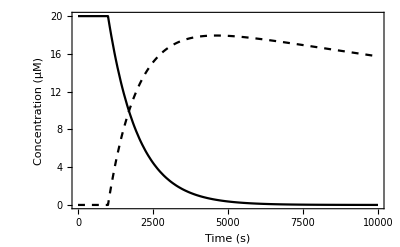

```mathematica
(*PIP2 Model*)

kiPIP=1/1000 Boole[t>1000];
kii=0.03/1000;
PIP2DAGModel=NDSolve[{PIP2'[t]==-PIP2[t] kiPIP,
DAG'[t]==PIP2[t] kiPIP -kii DAG[t] ,
PIP2[0]==20,
DAG[0]==0.0000001},
{PIP2,DAG},
{t,0,10000}
]

PIPPlot=Plot[{PIP2[t]/.PIP2DAGModel,DAG[t]/.PIP2DAGModel},{t,0,10000},PlotStyle->{Black,{Black,Dashed}}(*,PlotLegends->{"PIP_2","DAG"}*),Axes->False,Frame->True,FrameLabel->{"Time (s)","Concentration (µM)"}]
```

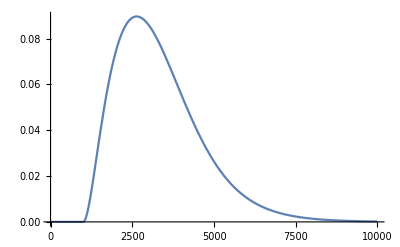

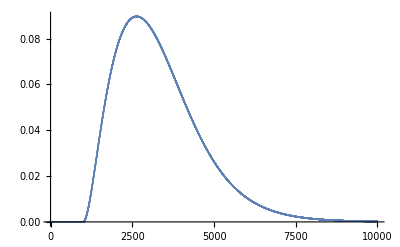

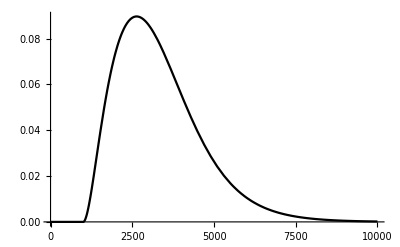

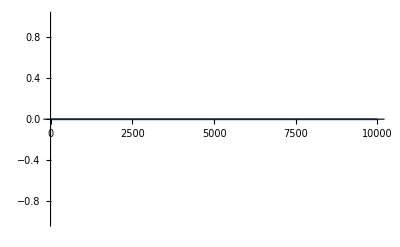

```mathematica
(*TRPC6*)
(*DAG and PIP2 depletion only model*)

(*TRPC parameters*)
(*DAG1,uM*)
K1pip=39;
(*DAG2, uM*)
K2pip=29;
(*PIP2,uM*)
K3pip=1.9;

(*Done in a complicated way because it wouldn't work otherwise*)
pTRPCspd=1/(K1pip K2pip/DAG[t]^2 +K2pip/DAG[t] +
(K1pip K2pip /DAG[t]^2)(K3pip/PIP2[t])+
K2pip (K3pip/PIP2[t])/DAG[t] +( K3pip/PIP2[t])+1);
Plot[pTRPCspd/.PIP2DAGModel,{t,0,10000}]

pTRPC6listdata=Table[{i,(pTRPCspd/.PIP2DAGModel)[[1]]/.t->i},{i,0,10000}];
ListPlot[pTRPC6listdata]
pTRPC6Fun=Interpolation[pTRPC6listdata];
Plot[pTRPC6Fun[t],{t,0,10000},PlotStyle->Black]

KTRPC6=0.0;
(*TRPC6*)
gTRPC6=35;

ITRPC6=gTRPC6 KTRPC6 pTRPC6Fun[t](v[t]-ECa);

Plot[ITRPC6/.v[t]->-60,{t,0,10000}]
```

{Boole[t>1000] InterpolatingFunction[…][t]}

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

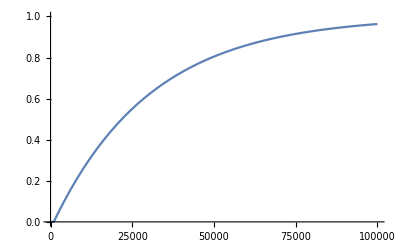

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction[{{0., 100000.}}, <>]

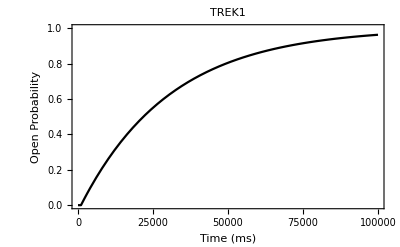

88.5 KTREK (80+v[t]) InterpolatingFunction[{{0., 100000.}}, <>][t]

```mathematica
tauTREK1=30000;

TREKmod=NDSolve[{PTREK1'[t]==(1-PTREK1[t])/tauTREK1,PTREK1[1000]==0},{PTREK1},{t,1000,100000}];


PTREK=Boole[t>1000]PTREK1[t]/.TREKmod

Plot[PTREK,{t,0,100000},PlotRange->{0,1}]
PTREKlist=Table[{t,PTREK[[1]]},{t,0,100000}];
PTREKFun=Interpolation[PTREKlist]
Plot[PTREKFun[t],{t,0,100000},PlotRange->{0,1},Axes->False,Frame->True,FrameLabel->{"Time (ms)","Open Probability"},PlotStyle->Black,PlotLabel->"TREK1"]
gTREK=88.5;
EK=-80;
ITrek=gTREK KTREK PTREKFun[t](v[t]-EK)
```

```mathematica
(*Unitary Conductances, pS*)
(*Calcium Channels*)
gTtype=8;
gLtype=25;

(*Big Potassium, Ca + Voltage sensitive*)
gBK=289;
gBKbeta1=289;
gBKbeta3=289;
gBKbeta4=289;

(*Voltage gated Potassium*)
gKv21=8.5;
gKv61=12.5;
gKv93=14.5;
gKv34=14;
gKv41=5;
gKv43=5;
gKv43b=5;
gKv43d=5;
gKv43KCNE3=5;
gKv43KK=5;
gKv71=1.8;
gKv74=2.1;
gherg=2;

(*Calcium sensitive Potassium*)
gSK2=2;
gSK3=2;
gSK4=11; 

(*ANO1*)
gANO1=7.5;
```

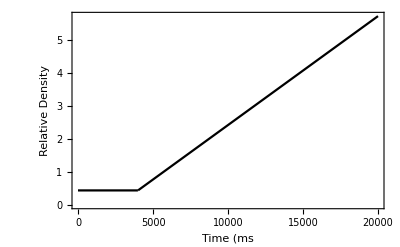

```mathematica
(*Function for increasing channel Densities*)
Tkinstart=4000;
kFun=1+0.00075*Boole[t>Tkinstart](t-Tkinstart);
Plot[0.44kFun,{t,0,20000},Axes->False,Frame->True,FrameLabel->{"Time (ms","Relative\nDensity"},PlotStyle->Black]
```

```mathematica
(*Channel Densities*)
KappaVec=(*{0.011704653576433877,0.0022733575751367322,0.015710550930122014,1.2870398271760902*^-6,4.425914277753245,0.4766057186062612,2.412948674617189,0.28379934895373515,10.445445339169765,0.2748803576191253,0.8706971791952244,1.6607626339021329,11.279143044615028,100.83133654689532,0.3316195690097338,0.0725710508417237,0.019790079603483713,0.04362898755385499,0.030983534520614624,0.0023127674284158946,27,0.1739864992504686}*)(*{0.00040067020680968016,0.09762521038960423,0.3587440204919744,0.013034731053677088,9.071415730812785,1.7178883416977786,6.784189439774919,1.7395097486619262,0.4431865954783055,4.190762232148571,0.5625555360108415,0.5140688110677819,1.605196148739609,76.47395300534959,1.5282579820339264,1.111882915209917,0.47575547849022415,0.9618572399062573,0.6613072348747572,0.19158997109337442,34.64487870706457,0.480047747889083}*)
(*This one works for KLCa-10.5:*) 
{0.9285538864372189,0.21386383415385268,0.4262270742022186,0.0031685216199145525,3.3471586805622087,2.0367586707871483,9.548758666722717,0.5464634153741685,1.0760366022533032,1.353815279009153,0.8785502558123907,0.8615609010324043,0.6647290615202367,0.3615831048715507,0.46994471156253875,1.3808775954842094,0.4424858403329093,0.9756229505405939,0.5457134302312829,0.11988169684292503,39.48801078038617,1.6794792098456508};
(*{2.27374*10^-13,3.55271*10^-15,-2.84217*10^-14,2.22045*10^-15,2.47036,2.43071,7.39409,9.66286,114,5.68434*10^-14,15,10,191,10.6927,-1.7053*10^-13,-2.84217*10^-14,2.84217*10^-14,4.26326*10^-14,-1.27676*10^-15,0.628217,32.2753,1.06581*10^-14};*)
(*Flatten[Import["/Users/joedunford/Documents/New Modelling/NewKappas.csv"]];*)


KTtype=4.5;
KLtype=10.5(*10.5*);

KBK=KappaVec[[1]];
KBKbeta1=KappaVec[[2]];
KBKbeta3=KappaVec[[3]];
KBKbeta4=KappaVec[[4]];

K21=KappaVec[[5]];
K61=KappaVec[[6]];
K93=KappaVec[[7]];
K34=KappaVec[[8]];
K41=KappaVec[[9]];

K43=KappaVec[[10]];
K43b=KappaVec[[11]];
K43d=KappaVec[[12]];
K43KCNE3=KappaVec[[13]];
K43KK=KappaVec[[14]];

K71=KappaVec[[15]];
K74=KappaVec[[16]];
Kherg=(*kFun**)KappaVec[[17]];

(*Calcium sensitive Potassium*)
KSK2=KappaVec[[18]];
KSK3=KappaVec[[19]];
KSK4=KappaVec[[20]]; 

(*ANO1*)
KANO1=0;

KKleak=KappaVec[[22]];

KTREK=0.055;
```

```mathematica
Channels={
{"L-type Ca", LtypeMC, {0,0,0,0,0,0,0,1},1,gLtype,ECa,KLtype,LCa[t],,,LCa},
{"T-type Ca" ,TtypeMC, {0,0,0,1},1,gTtype,ECa,KTtype,TCa[t],,,TCa},
{"BK alpha",BKMC,{0,1},1,gBK,EK,KBK,BK[t],,,BK},
{"BK Beta 1",BKbeta1MC,{0,1},1,gBKbeta1,EK,KBKbeta1,BKb1[t],,,BKb1},
{"BK Beta 3", BKbeta3MC,{0,0,0,0,0,1,1,1,1,1,0,0,0,0,0},1,gBKbeta3,EK,KBKbeta3,BKb3[t],,,BKb3},
{"BK Beta 4", BKbeta4MC, {0,1},1,gBKbeta4,EK,KBKbeta4,BKb4[t],,,BKb4},
{"Kv2.1", Kv21DELG18mat2, {0,0,0,0,0,0,0,0,0,0,0,0,1},1,gKv21,EK,K21,Kv21[t],,,Kv21},
{"Kv2.1/6.1", Kv2161MC,{0,0,0,1},1,gKv61,EK,K61,Kv61[t],,,Kv61},
{"Kv2.1/9.3", Kv93MC, {0,0,0,1,0,0,0,1},1,gKv93,EK,K93,Kv93[t],,,Kv93},
{"Kv3.4", Kv34MC, {0,0,0,1},1,gKv34,EK,K34,Kv34[t],,,Kv34},
{"Kv4.1", Kv41MC, {0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},1,gKv41,EK,K41,Kv41[t],,,Kv41},
{"Kv4.3", Kv43Mat, {0,0,0,0,0,0,0,0,0,0,0,0,1},1,gKv43,EK,K43,Kv43[t],,,Kv43},
{"Kv4.3+KChIP2b",Kv43bMC,{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},1,gKv43b,EK,K43b,Kv43b[t],,,Kv43b},
{"Kv4.3+KChIP2d",Kv43dMC,{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},1,gKv43d,EK,K43d,Kv43d[t],,,Kv43d},
{"Kv4.3+KCNE3",Kv43KCNE3MC,{0,0,0,0,0,0,0,1},1,gKv43KCNE3,EK,K43KCNE3,Kv43K[t],,,Kv43K},
{"Kv4.3+ KChIP2b+KCNE3", Kv43KKMC,{0,0,0,0,0,0,0,1},1,gKv43KK,EK,K43KK,Kv43KK[t],,,Kv43KK},
{"Kv7.1", Kv71Mat, {0,0,1,1,0},1,gKv71,EK,K71,Kv71[t],,,Kv71},
{"Kv7.4", Kv74MC, {0,0,0,1},1,gKv74,EK,K74,Kv74[t],,,Kv74},
{"Kv11.1/hERG", hERGMC, {0,0,0,1,0},1,gherg,EK,Kherg,hERG[t],,,hERG},
{"SK2",SK2MC,{0,1},1,gSK2,EK,KSK2,SK2[t],,,SK2},
{"SK3",SK3MC,{0,1},1,gSK3,EK,KSK3,SK3[t],,,SK3},
{"SK4",SK4MC,{0,1},1,gSK4,EK,KSK4,SK4[t],,,SK4},
{"ANO1" (*Contreras-Vite mod*), ANO1MC,{0,0,0,0,0,0,1,1,1,1,1,1},-1,gANO1,ECl,KANO1,ANO1[t],,,ANO1}
};
```

```mathematica
(*Open states*)

OLCa= {0,0,0,1};(*{0,0,0,0,0,0,0,1};*)
OTCa= {0,0,0,1};

OBK={0,1};
OBKb1={0,1};
OBKb3={0,0,0,0,0,1,1,1,1,1,0,0,0,0,0};
OBKb4={0,1};

OKv21={0,0,0,0,0,0,0,0,0,0,0,0,1};
OKv61={0,0,0,1};
OKv93= {0,0,0,1,0,0,0,1};
OKv34={0,0,0,1};
OKv41={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1};
OKv43={0,0,0,0,0,0,0,0,0,0,0,0,1};
OKv43b={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1};
OKv43d={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1};
OKv43KCNE3={0,0,0,0,0,0,0,1};
OKv43KK={0,0,0,0,0,0,0,1};
OKv71= {0,0,1,1,0};
OKv74={0,0,0,1};
OhERG= {0,0,0,1,0};

OSK2={0,1};
OSK3={0,1};
OSK4={0,1};

OANO1={0,0,0,0,0,0,1,1,1,1,1,1};
```

```mathematica
(*Starting Steady States*)

VStart=-59;
CaStart=84;
CaSRstart=1000;


LCass0=Last[Eigenvectors[LtypeMC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[LtypeMC/.{v[t]->VStart,Ca[t]->CaStart}]]];
TCass0=Last[Eigenvectors[TtypeMC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[TtypeMC/.{v[t]->VStart,Ca[t]->CaStart}]]];

BKss0=Last[Eigenvectors[BKMC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[BKMC/.{v[t]->VStart,Ca[t]->CaStart}]]];
BKbeta1ss0=Last[Eigenvectors[BKbeta1MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[BKbeta1MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
BKbeta3ss0=Last[Eigenvectors[BKbeta3MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[BKbeta3MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
BKbeta4ss0=Last[Eigenvectors[BKbeta4MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[BKbeta4MC/.{v[t]->VStart,Ca[t]->CaStart}]]];

Kv21ss0=Last[Eigenvectors[Kv21DELG18mat2/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv21DELG18mat2/.{v[t]->VStart,Ca[t]->CaStart}]]];
Kv61ss0=Last[Eigenvectors[Kv2161MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv2161MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
Kv93ss0=Last[Eigenvectors[Kv93MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv93MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
Kv34ss0=Last[Eigenvectors[Kv34MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv34MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
Kv41ss0=Last[Eigenvectors[Kv41MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv41MC/.{v[t]->VStart,Ca[t]->CaStart}]]];

Kv43ss0=Last[Eigenvectors[Kv43Mat/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv43Mat/.{v[t]->VStart,Ca[t]->CaStart}]]];
Kv43bss0=Last[Eigenvectors[Kv43bMC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv43bMC/.{v[t]->VStart,Ca[t]->CaStart}]]];
Kv43dss0=Last[Eigenvectors[Kv43dMC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv43dMC/.{v[t]->VStart,Ca[t]->CaStart}]]];
Kv43KCNE3ss0=Last[Eigenvectors[Kv43KCNE3MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv43KCNE3MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
Kv43KKss0=Last[Eigenvectors[Kv43KKMC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv43KKMC/.{v[t]->VStart,Ca[t]->CaStart}]]];

Kv71ss0=Last[Eigenvectors[Kv71Mat/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv71Mat/.{v[t]->VStart,Ca[t]->CaStart}]]];
Kv74ss0=Last[Eigenvectors[Kv74MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[Kv74MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
hERGss0=Last[Eigenvectors[hERGMC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[hERGMC/.{v[t]->VStart,Ca[t]->CaStart}]]];

SK2ss0=Last[Eigenvectors[SK2MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[SK2MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
SK3ss0=Last[Eigenvectors[SK3MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[SK3MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
SK4ss0=Last[Eigenvectors[SK4MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[SK4MC/.{v[t]->VStart,Ca[t]->CaStart}]]];

ANO1ss0=Last[Eigenvectors[ANO1MC/.{v[t]->VStart,Ca[t]->CaStart}]]/Total[Last[Eigenvectors[ANO1MC/.{v[t]->VStart,Ca[t]->CaStart}]]];
```

```mathematica
(*Currents*)

ILCa=gLtype KLtype LCa[t].OLCa(v[t]-ECa);
ITCa=gTtype KTtype TCa[t].OTCa(v[t]-ECa);

IBK=gBK KBK BK[t].OBK(v[t]-EK);
IBKb1=gBKbeta1 KBKbeta1 BKbeta1[t].OBKb1(v[t]-EK);
IBKb3=gBKbeta3 KBKbeta3 BKbeta3[t].OBKb3(v[t]-EK);
IBKb4=gBKbeta4 KBKbeta4 BKbeta4[t].OBKb4(v[t]-EK);

IKv21=gKv21 K21 Kv21[t].OKv21(v[t]-EK);
IKv61=gKv61 K61 Kv61[t].OKv61(v[t]-EK);
IKv93=gKv93 K93 Kv93[t].OKv93(v[t]-EK);
IKv34=gKv34 K34 Kv34[t].OKv34(v[t]-EK);
IKv41=gKv41 K41 Kv41[t].OKv41(v[t]-EK);

IKv43=gKv43 K43 Kv43[t].OKv43(v[t]-EK);
IKv43b=gKv43b K43b Kv43b[t].OKv43b(v[t]-EK);
IKv43d=gKv43d K43d Kv43d[t].OKv43d(v[t]-EK);
IKv43KCNE3=gKv43KCNE3 K43KCNE3 Kv43KCNE3[t].OKv43KCNE3(v[t]-EK);
IKv43KK=gKv43KK K43KK Kv43KK[t].OKv43KK(v[t]-EK);

IKv71=gKv71 K71 Kv71[t].OKv71(v[t]-EK);
IKv74=gKv74 K74 Kv74[t].OKv74(v[t]-EK);
IhERG=gherg Kherg hERG[t].OhERG(v[t]-EK);

ISK2=gSK2 KSK2 SK2[t].OSK2(v[t]-EK);
ISK3=gSK3 KSK3 SK3[t].OSK3(v[t]-EK);
ISK4=gSK4 KSK4 SK4[t].OSK4(v[t]-EK);

IANO1=gANO1 KANO1 ANO1[t].OANO1(v[t]-ECl);

IKleak= KKleak(v[t]-EK);
```

```mathematica
RTOF=r Temp/f;
r=8.314472*10^3;
Temp=310.0;
f=9.6485309*10^4;

EK=-80;
ECl=-20;
Caout=1.8; (*Extracellular Calcium, mM*)
ECa=(RTOF/2) Log[1000Caout/(Ca[t]/1000)];


TMin=0;
TMax=100000;
TVals2=Range[TMin,TMax];
(*v[t]=-20;*)
(*Ca[t]=500;*)
```

```mathematica
Iinj=-150*Boole[t>1000&&t<4000];
```

```mathematica
Model=NDSolve[
{v'[t]==-0.001*
(ILCa+ITCa+
IBK+IBKb1+IBKb3+IBKb4+
IKv21+IKv61+IKv93+IKv34+IKv41+
IKv43+IKv43b+IKv43d+IKv43KCNE3+IKv43KK+
IKv71+IKv74+IhERG+
ISK2+ISK3+ISK4+
IANO1+
IKleak+
Inak+INaCa
+Iinj+ITrek
(*+ITRPC6*) 
)
,
Ca'[t]==JCa-JpmCa-JNaCa-V2/ScaleFactor+V3/ScaleFactor+CaSR[t] kf/ScaleFactor ,
CaSR'[t]==ScaleFactor(V2-V3-kf CaSR[t]),
LCa'[t]==LtypeMC.LCa[t],
TCa'[t]==TtypeMC.TCa[t],

BK'[t]==BKMC.BK[t],
BKbeta1'[t]==BKbeta1MC.BKbeta1[t],
BKbeta3'[t]==BKbeta3MC.BKbeta3[t],
BKbeta4'[t]==BKbeta4MC.BKbeta4[t],

Kv21'[t]==Kv21DELG18mat2.Kv21[t],
Kv61'[t]==Kv2161MC.Kv61[t],
Kv93'[t]==Kv93MC.Kv93[t],
Kv34'[t]==Kv34MC.Kv34[t],
Kv41'[t]==Kv41MC.Kv41[t],
Kv43'[t]==Kv43Mat.Kv43[t],
Kv43b'[t]==Kv43bMC.Kv43b[t],
Kv43d'[t]==Kv43dMC.Kv43d[t],
Kv43KCNE3'[t]==Kv43KCNE3MC.Kv43KCNE3[t],
Kv43KK'[t]==Kv43KKMC.Kv43KK[t],
Kv71'[t]==Kv71Mat.Kv71[t],
Kv74'[t]==Kv74MC.Kv74[t],
hERG'[t]==hERGMC.hERG[t],

SK2'[t]==SK2MC.SK2[t],
SK3'[t]==SK3MC.SK3[t],
SK4'[t]==SK4MC.SK4[t],

ANO1'[t]==ANO1MC.ANO1[t],

v[0]==VStart,
Ca[0]==CaStart,
CaSR[0]==CaSRstart,
LCa[0]==LCass0,
TCa[0]==TCass0,

BK[0]==BKss0,
BKbeta1[0]==BKbeta1ss0,
BKbeta3[0]==BKbeta3ss0,
BKbeta4[0]==BKbeta4ss0,

Kv21[0]==Kv21ss0,
Kv61[0]==Kv61ss0,
Kv93[0]==Kv93ss0,
Kv34[0]==Kv34ss0,
Kv41[0]==Kv41ss0,

Kv43[0]==Kv43ss0,
Kv43b[0]==Kv43bss0,
Kv43d[0]==Kv43dss0,
Kv43KCNE3[0]==Kv43KCNE3ss0,
Kv43KK[0]==Kv43KKss0,

Kv71[0]==Kv71ss0,
Kv74[0]==Kv74ss0,
hERG[0]==hERGss0,

SK2[0]==SK2ss0,
SK3[0]==SK3ss0,
SK4[0]==SK4ss0,

ANO1[0]==ANO1ss0
},
{v,
Ca,CaSR,
LCa,TCa,
BK, BKbeta1, BKbeta3, BKbeta4,
Kv21, Kv61,Kv93,Kv34,Kv41,
Kv43,Kv43b,Kv43d,Kv43KCNE3,Kv43KK,
Kv71,Kv74,hERG,
SK2,SK3,SK4,
ANO1
},
{t,TMin,TMax},
MaxSteps->Infinity
]
```

{{v→InterpolatingFunction[{{0., 100000.}}, <>],Ca→InterpolatingFunction[{{0., 100000.}}, <>],CaSR→InterpolatingFunction[{{0., 100000.}}, <>],LCa→InterpolatingFunction[{{0., 100000.}}, <>],TCa→InterpolatingFunction[{{0., 100000.}}, <>],BK→InterpolatingFunction[{{0., 100000.}}, <>],BKbeta1→InterpolatingFunction[{{0., 100000.}}, <>],BKbeta3→InterpolatingFunction[{{0., 100000.}}, <>],BKbeta4→InterpolatingFunction[{{0., 100000.}}, <>],Kv21→InterpolatingFunction[{{0., 100000.}}, <>],Kv61→InterpolatingFunction[{{0., 100000.}}, <>],Kv93→InterpolatingFunction[{{0., 100000.}}, <>],Kv34→InterpolatingFunction[{{0., 100000.}}, <>],Kv41→InterpolatingFunction[{{0., 100000.}}, <>],Kv43→InterpolatingFunction[{{0., 100000.}}, <>],Kv43b→InterpolatingFunction[{{0., 100000.}}, <>],Kv43d→InterpolatingFunction[{{0., 100000.}}, <>],Kv43KCNE3→InterpolatingFunction[{{0., 100000.}}, <>],Kv43KK→InterpolatingFunction[{{0., 100000.}}, <>],Kv71→InterpolatingFunction[{{0., 100000.}}, <>],Kv74→InterpolatingFunction[{{0., 100000.}}, <>],hERG→InterpolatingFunction[{{0., 100000.}}, <>],SK2→InterpolatingFunction[{{0., 100000.}}, <>],SK3→InterpolatingFunction[{{0., 100000.}}, <>],SK4→InterpolatingFunction[{{0., 100000.}}, <>],ANO1→InterpolatingFunction[{{0., 100000.}}, <>]}}

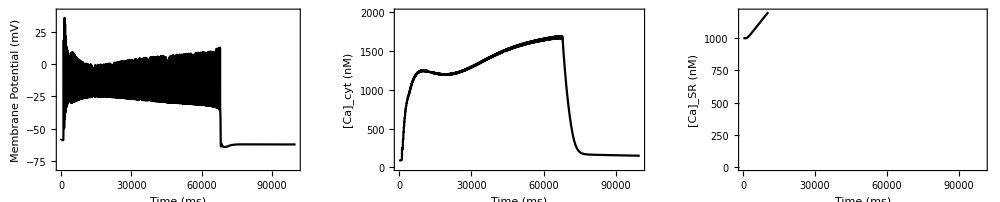

```mathematica
CaPlot=Plot[Ca[t]/.Model,{t,0,TMax},PlotRange->{0,2000},PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","[Ca]_cyt (nM)"}];
CaSRPlot=Plot[CaSR[t]/.Model,{t,0,TMax},PlotRange->{0,1200},PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","[Ca]_SR (nM)"}];
VPlot=Plot[v[t]/.Model,{t,0,TMax},PlotRange->{-80,40},PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Membrane Potential (mV)"}];
GraphicsRow[{VPlot,CaPlot,CaSRPlot},ImageSize->1000]
```

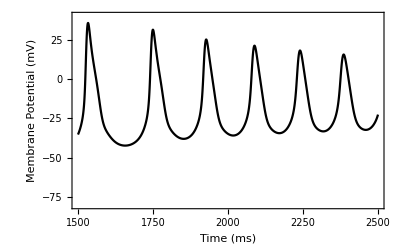

```mathematica
Plot[v[t]/.Model,{t,1500,2500},PlotRange->{-80,40},PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Membrane Potential (mV)"}]
```

```mathematica
2.6*39
```

101.4

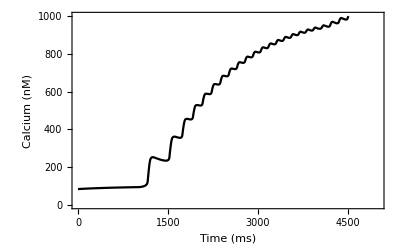

```mathematica
Plot[Ca[t]/.Model,{t,00,5000},PlotRange->{0,1000},PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Calcium (nM)"}]
```

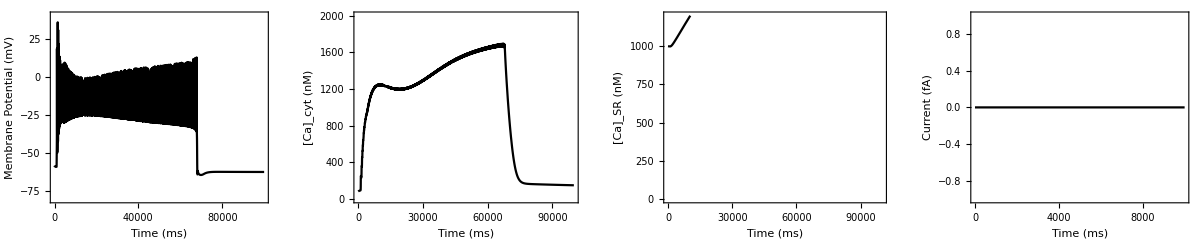

```mathematica
ANO1Plot=Plot[IANO1/.Model,{t,0,10000},PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Current (fA)"}];

GraphicsRow[{VPlot,CaPlot,CaSRPlot,ANO1Plot},ImageSize->1200]
```

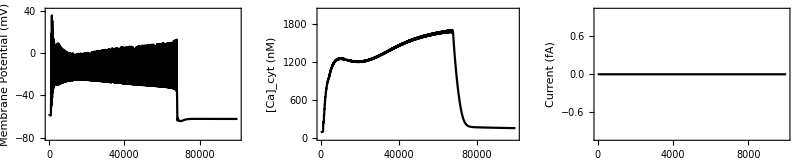

```mathematica
GraphicsRow[{VPlot,CaPlot,Plot[ITRPC6/.Model,{t,0,10000},PlotRange->Full,PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Current (fA)"}]},ImageSize->800]
```

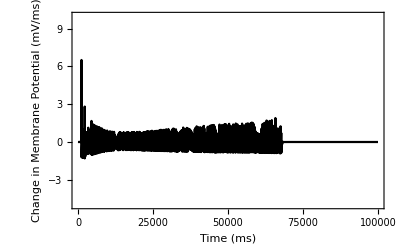

```mathematica
Plot[v'[t]/.Model,{t,0,TMax},PlotRange->{-5,10},PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Change in Membrane\nPotential (mV/ms)"}]
```

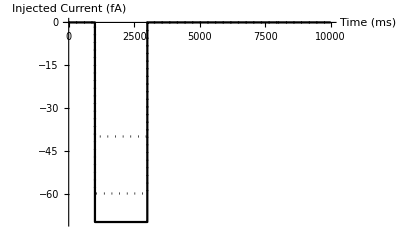

```mathematica
Pulse1=Table[-70Boole[t>1000&&t<3000],{t,0,10000}];
Pulse2=Table[-60Boole[t>1000&&t<3000],{t,0,10000}];
Pulse3=Table[-40Boole[t>1000&&t<3000],{t,0,10000}];
Show[ListPlot[Pulse1,PlotStyle->Black,Joined->True, AxesLabel->{"Time (ms)","Injected Current (fA)"}],ListPlot[Pulse2,PlotStyle->{Black,Dotted},Joined->True],ListPlot[Pulse3,PlotStyle->{Black,Dotted},Joined->True]]
```

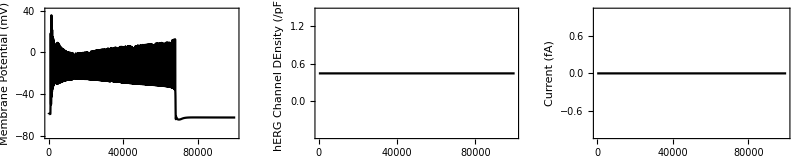

```mathematica
GraphicsRow[{VPlot,Plot[Kherg/.Model,{t,0,TMax},PlotRange->Full,PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","hERG Channel\nDEnsity (/pF)"}],Plot[IANO1/.Model,{t,0,TMax},PlotRange->Full,PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Current (fA)"}]},ImageSize->800]
```

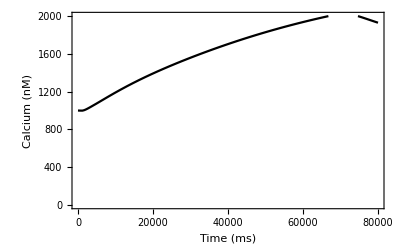

```mathematica
Plot[CaSR[t]/.Model,{t,00,80000},PlotRange->{0,2000},PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Calcium (nM)"}]
```

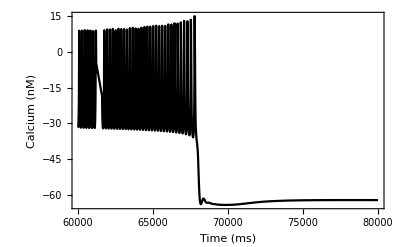

```mathematica
Plot[v[t]/.Model,{t,60000,80000},PlotRange->Full,PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Calcium (nM)"}]
```

```mathematica
7*140
```

980

```mathematica
0.3*140
```

42.

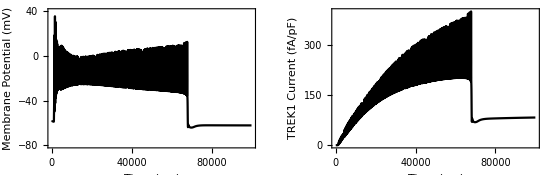

```mathematica
GraphicsRow[{VPlot,Plot[ITrek/.Model,{t,0,TMax},PlotRange->Full,PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","TREK1 Current (fA/pF)"}]},ImageSize->550]
```

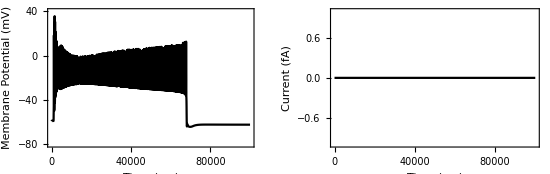

```mathematica
GraphicsRow[{VPlot,Plot[IANO1/.Model,{t,0,TMax},PlotRange->Full,PlotStyle->Black,Axes->False,Frame->True,FrameLabel->{"Time (ms)","Current (fA)"}]},ImageSize->550]
```